# Kalman Folding, Expanded and Extended

Brian Beckman
Dec 2023

## Abstract

In an earlier notebook (https://community.wolfram.com/groups/-/m/t/3078712), we introduced Kalman Estimation or Filtering as a functional fold. Fold decouples accumulation activity from the source of data. The same foldable works over data in memory, over streams computed on-the-fly, and over external observations delivered asynchronously. Foldable form confers a great advantage on Kalman techniques. It is established that Kalman estimators run in constant memory, but with foldable form, they can be rigorously tested offline in friendly environments with ground truth.

Here, we demonstrate Fold over multiple kinds of Kalman estimator, from time-dependent dynamical models through linearized Extended Kalman Filtering, both of which are foundational, critical technology. We also investigate five different forms for the covariance update, each with different numerical hazards.

We use the Wolfram language because it excels at concise expression of mathematical codes. The same ideas can be rendered in any contemporary programming language with minimal support for closures, such as Python, C++, and Java. The approach of the paper is pedagogical with many examples fully worked out.

## Preliminaries

## Definitions

### Abbreviations

obl | observable
obr | observer
obn | observation

### Notations

```mathematica
<<"Notation`"
InfixNotation[⊕,Join];
```

### Utility Functions

gen generates random samples from a covariance matrix. It only honors the diagonal terms, but each individually.

```mathematica
ClearAll[col,row,id,con,zero,len,dim,m,f1,d1,inv,pinv,scalar,groundTruth,randn,gen,dump,pick];
id=IdentityMatrix;
con[c_,m_,n_]:=ConstantArray[c,{m,n}];
con[c_,n_]:=con[c,n,n];
zero[m_,n_]:=con[0.,m,n];
zero[n_]:=con[0.,n];
col[xs_List]:=List/@xs;
col[c_,n_]:=con[c,n,1];
row[xs_List]:=List[xs];
row[c_,n_]:=con[c,1,n];
len=Length;
dim[squareMatrix_List]:=len[squareMatrix⟦1⟧];
m=MatrixForm;
f1=Flatten[#,1]&;
d1=Drop[#,1]&;
inv=Inverse;
pinv=PseudoInverse;
scalar[m1x1_]:=m1x1⟦1,1⟧;
dump[x_]:=(Print[x];x);
groundTruth=({{-3}, {9}, {-4}, {-5}});
pick[n_]:=#⟦n⟧&;
pick[m_,n_]:=#⟦m,n⟧&
randn[σ_:1.0]:=
If[Chop@σ==0.0,0.0,
RandomVariate[NormalDistribution[0.0,σ]]];
(* generate a random sample from a covariance matrix *)
gen[P_]:=
Module[{σs},
σs=Sqrt/@Table[P⟦i,i⟧,{i,dim[P]}];
randn/@σs];
```

## Utility Code for Displays: Experiment

TODO: Limitation: scalar observations only.

```mathematica
ClearAll[experiment,experiment1,withTimes,myStyle,stats];
withTimes[times_,obj_]:=MapThread[List,{times,obj}];
myStyle[s_String]:=Style[s,FontFamily->"Candara",FontSize->12];
stats[nym_String,ress_List,σs_List,predictedVariance_:0]:=
Module[{nonNegss,negss},
{negss,nonNegss}=
(* SplitBy doesn't return the required shapes when all the data have the same sign. *)
(* e.g., SplitBy[{-3,-2,-1},Negative] produces {{-3,-2,-1}}, but we need {{-3,-2,-1},{}} *)
(* lest nonNegss not have any value and the destructuring assignment fail with a message. *)
(* SplitBy[Sort[Abs[ress]-σs],#≥0&; *)
(* Some computations produce negative sigma^2 by floating-point error. We do not have a 
principled way to treat those. We'll just filter them out. *)
With[{pairs=Select[MapThread[List,{Abs[ress],σs}],Im[#⟦2⟧]==0&]},
With[{xs=#1-#2&@@@pairs},
{Select[xs,Negative],Select[xs,#≥0&]}]];
(*Print[<|"ress"->ress,"σs"->σs,"Abs[ress]-σs"->Abs[ress]-σs,
"sortedRess"->Sort[Abs[ress]-σs],
"splittedRess"->SplitBy[Sort[Abs[ress]-σs],#≥0&]|>];*)
Grid[{
{"% "<>nym<>" resids < σ (Expect >= 68)",100.0Length[negss]/Length[ress]},
{nym<>" resids >= σ",1.0Length[nonNegss]},
{nym<>" resids < σ",1.0Length[negss]},
{"average "<>nym<>" resid",Mean[ress]},
{"theoretical std dev",Sqrt@predictedVariance},
{"std dev of "<> nym<>" resids",StandardDeviation[ress]}},
Frame->All]];

experiment1[
startTime_,
endTime_,
timeIncrement_,
aPrioriState_,
aPrioriCovariance_,
observationNoiseCovariance_,
fakeFn_,
trueObservationFn_,
iterations_Integer:1]:=
Module[{t,timesIter,times,fakes,estss,
truePositions,
estimatedPositionss,
positionResidualss,
positionStandardDeviationss,
predictedVariance,
positionStats},
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
truePositions=Table[trueObservationFn[t],Evaluate@timesIter];
fakes[]:=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
estss=Table[
FoldList[
kalman[observationNoiseCovariance],
{aPrioriState,aPrioriCovariance},
fakes[]],iterations];
(* starts at 2;; to skip the a-priori *)
estimatedPositionss=estss⟦;;,2;;,1,1,1⟧;
predictedVariance=Last[estss⟦1⟧]⟦2,1,1⟧;
positionResidualss=truePositions-#&/@estimatedPositionss;
positionStandardDeviationss=Sqrt@estss⟦;;,2;;,2,1,1⟧;
positionStats=stats["position",
f1@positionResidualss,f1@positionStandardDeviationss,predictedVariance];
Grid@{{ListLinePlot[
(withTimes[times,#]&/@positionResidualss)⊕
(withTimes[times,#]&/@positionStandardDeviationss)⊕
(withTimes[times,#]&/@-positionStandardDeviationss),
Frame->True,
FrameLabel->{{
myStyle@"Residual",""},{
myStyle@"time / sec",
myStyle@"Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]},
{ListLinePlot[{withTimes[times,truePositions]}⊕
(withTimes[times,#]&/@estimatedPositionss),
Frame->True,
FrameLabel->{{
myStyle@"Estimate x",""},{
myStyle@"time / sec",
myStyle@"Truth and Estimates vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]},
{positionStats}
}];

experiment[
startTime_,
endTime_,
timeIncrement_,
aPrioriState_,
aPrioriCovariance_,
observationNoiseCovariance_,
fakeFn_,
trueObservationFn_,
trueObservationDerivativeFn_,
iterations_Integer:1]:=
Module[{t,timesIter,times,fakes,estss,
truePositions,trueSpeeds,
estimatedPositionss,estimatedSpeedss,
positionResidualss,speedResidualss,
positionStandardDeviationss,speedStandardDeviationss,
theoreticalPositionVariance,
theoreticalSpeedVariance,
positionStats,speedStats},
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
truePositions=Table[trueObservationFn[t],Evaluate@timesIter];
trueSpeeds=Table[trueObservationDerivativeFn[t],Evaluate@timesIter];
fakes[]:=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
estss=Table[
FoldList[
kalman[observationNoiseCovariance],
{aPrioriState,aPrioriCovariance},
fakes[]],iterations];
(* starts at 2;; to skip the a-priori *)
estimatedPositionss=estss⟦;;,2;;,1,1,1⟧;
estimatedSpeedss=estss⟦;;,2;;,1,2,1⟧;
positionResidualss=truePositions-#&/@estimatedPositionss;
speedResidualss=trueSpeeds-#&/@estimatedSpeedss;
positionStandardDeviationss=Sqrt@estss⟦;;,2;;,2,1,1⟧;
speedStandardDeviationss=Sqrt@estss⟦;;,2;;,2,2,2⟧;
theoreticalPositionVariance=Last[estss⟦1⟧]⟦2,1,1⟧;
theoreticalSpeedVariance=Last[estss⟦1⟧]⟦2,2,2⟧;
positionStats=stats["position",f1@positionResidualss,f1@positionStandardDeviationss,theoreticalPositionVariance];
speedStats=stats["speed",f1@speedResidualss,f1@speedStandardDeviationss,theoreticalSpeedVariance];
Grid@{{ListLinePlot[
(withTimes[times,#]&/@positionResidualss)⊕
(withTimes[times,#]&/@positionStandardDeviationss)⊕
(withTimes[times,#]&/@-positionStandardDeviationss),
Frame->True,
FrameLabel->{{
myStyle@"Position Residual / foot",""},{
myStyle@"time / sec",
myStyle@"Position Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[
(withTimes[times,#]&/@speedResidualss)⊕
(withTimes[times,#]&/@speedStandardDeviationss)⊕
(withTimes[times,#]&/@-speedStandardDeviationss),
Frame->True,
FrameLabel->{{
myStyle@"Speed Residual / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]},
{ListLinePlot[{withTimes[times,truePositions]}⊕
(withTimes[times,#]&/@estimatedPositionss),
Frame->True,
FrameLabel->{{
myStyle@"Position / foot",""},{
myStyle@"time / sec",
myStyle@"Position Truth and Estimates vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[{withTimes[times,trueSpeeds]}⊕
(withTimes[times,#]&/@estimatedSpeedss),
Frame->True,
FrameLabel->{{
myStyle@"Speed / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Truth and Estimate.7fs vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]},
{positionStats,speedStats}
}];
```

## Preludes: Running Statistics

This section repeats material found in the earlier notebook, https://community.wolfram.com/groups/-/m/t/3078712. Skip this section if you are comfortable with recurrent forms for Variance and for Welford’s formula.

Running Count

Consider a sequence of samples of normally distributed noise with zero mean and unit variance. We calculate descriptive statistics of this sequence using Fold expressions that decouple iteration and accumulation from the means and manner of accessing the observations.

Make a concrete example.

```mathematica
ClearAll[zs];
zs=RandomVariate[NormalDistribution[],10]
```

{2.20925,1.6567,0.706944,-0.553308,-1.10676,0.938315,0.875102,-0.411259,-0.582858,-0.504342}

Running count, as a fold, is trivial.

```mathematica
ClearAll[cume];
cume[n_,z_]:=n+1;
Fold[cume,0,zs]
```

10

Running Mean

### Definition of Mean

As we accumulate data, one observation, z, at a time, write the new estimate of the mean as the ratio of (numerator) the current sum of all data plus the new observation z and (denominator) the new count, n+1. Write x or z̄ for the current estimate of the mean.

### Mean as a Fold

We use Mathematica’s built-in Fold to update a List, which appears in curly braces. This list is a packet of cumulative results. The first element of the packet is x, the current estimate of the mean. The second element is n, the current count of data. The third and last element is sum, the current sum of all input data. Fold accumulates the observations, z, one-at-a-time, from the list of all data, zs. The function cume is the foldable accumulator function, or just the foldable. It depends only on the current packet, {x,n,sum}, and on one datum z, from the list zs.

Fold takes three arguments: the foldable cume, an initial value for the result packet, {0, 0, 0}, and the list, zs, of all data. Fold is flexible; we show later a version that takes data from a real-time asynchronous source rather than from a list of data in memory, but re-uses the same cume.

### Why Fold is Important

The importance of this flexibility is just that: Fold can take data from anywhere. Here, Fold is in a friendly environment where we can test results in local computer memory against ground truth. Fold can also take data from somewhere else, say from a hostile environment without ground truth to compare against. We can test foldable functions like cume in the friendly environment, build up trust in foldables, and later deploy them in hostile environments with high assurance that they will not fail.

### Naively Folding the Definition of Mean

```mathematica
ClearAll[cume];
cume[{x_,n_,sum_},z_]:=
{(sum+z)/(n+1),n+1,sum+z};
Fold[cume,{0,0,0},zs]
```

{0.322779,10,3.22779}

Check against Mathematica built-in Mean function:

```mathematica
Mean[zs]
```

0.322779

### A Preferable Form

No need to track the running sum in the result packet. Express the new estimate of mean-so-far as the sum of the old estimate of mean-so-far and a correction. The correction depends only on old values of sum-of-data and count-of-data, and on a new datum, z.

The right-hand side of the recurrence formula z̄←z̄+K×(z-z̄) depends only on old values and the new datum z. The recurrence is not an equation because it has an arrow, ←, but it means the following equation: the new, (n+1)^th estimate of the mean equals the current, n^th estimate plus a correction. The correction is a gain, K, times the residual, (z_(n+1)-(z̄)_n). The residual is the difference between the current estimate, (z̄)_n or x, and the new datum, z_(n+1), i.e., “how far off the mark are we, so far?” In Equation 1, below, the mathematical notation for the recurrence is shown along with the "programming-language" formula.

(z̄)_(n+1)=(z̄)_n+K×(z_(n+1)-(z̄)_n)=x+K×(z_(n+1)-x).

Next we see a new foldable cume that expresses the new estimate as the old estimate plus the correction. We derive the gain factor immediately after checking this fold:

```mathematica
ClearAll[cume];
cume[{x_,n_},z_]:=
With[{K=1/(n+1)},
{x+K(z-x),n+1}];
Fold[cume,{0,0},zs]
```

{0.322779,10}

Algebraically, we reckon the gain, K, as follows. The sum of all data so far is, by the original definition, the current estimate x of the mean times the count n of data so far. We trust the earlier form of the new estimate of the mean, (sum + z)/(n+1), so write it as (x n+z)/(n+1). Set it equal to the new, desired form, x plus the correction K(z-x), and solve for K:

```mathematica
Solve[(x n + z)/(n+1)==x+K(z-x),K]
```

{{K→1/(1+n)}}

We prefer this form because (1) it separates old quantities on the right from new quantities on the left, except for the new datum, z on the right, and (2) it is easy to memorize. It is an affine update.

### The Kalman Update

The form above will become a mantra for all kinds of estimates:

The new estimate of any quantity is the sum of the old estimate and a gain times the residual of the old estimate and a new datum.

Equation 1 is formally identical.7f.7f to the update phase of any Kalman-type filter. This paper builds.7f up to several Kalman filters through a sequence of more elementary calculations that have similar forms.

Running Variance

### Definitions

Variance is a measure of volatility or dispersion. It is the sum of squared residuals of data with respect to the running mean, divided by the count less one. Recall that the .7fresidual is the difference between an observation z and the old mean x. The “count less one” is Bessel’s correction for sample statistics, not explained here.

Mathematica has a built-in Variance function that furnishes ground-truth for our calculations. Here is Mathematica’s variance over our friendly data set, zs.

```mathematica
Variance[zs]
```

1.22487

Variance is also standard deviation squared, and Mathematica has a built-in, ground-truth function for standard deviation:

```mathematica
StandardDeviation[zs]^2===Variance[zs]
```

True

### Variance in Kalman Form

#### Sum of Squared Residuals

Here is the sum of squared residuals,

Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2

We require it to be the variance times the length-less-one. Here is a fold that computes the sum of squared residuals, ssr. Notice that we must precompute and pass along the final mean. This is undesirable, and we fix it soon.

```mathematica
ClearAll[cume];
cume[{ssr_,finalMean_,n_},z_]:=
{ssr+(z-finalMean)^2,finalMean,n+1};
Fold[cume, {0,Mean[zs],0},zs]
```

{11.0239,0.322779,10}

However, despite the undesirable form, we got ssr right, according to Mathematica:

```mathematica
(* ssr *) Variance[zs]*(Length[zs]-1)
```

11.0239

#### Covariance

The covariance, for scalar data, is the same as the Variance. For vector data, the covariance is a matrix. We shall get there. For now, we just show that Mathematica’s built-in, Covariance, yields what we expect:

```mathematica
Covariance[zs]
```

1.22487

```mathematica
On[Assert];Assert[Covariance[zs]===Variance[zs]]
```

### Why Kalman Form is Important

We require a running covariance that does not refer to future observations (the final mean implicitly refers to all observations) and does not store the entire past, only a summary. In computer terms, storing only a summary of constant size, say in a slot in one of our data packets, is critically important. In this friendly example, we have ten data, and we can easily store them in memory. In a real-world, hostile environment, we will have an infinite stream of observations instead of our friendly zs. We might store a few million of them in memory and do fancy tricks with sliding windows over the data, but why do that when we can mathematically rewrite covariance in a foldable cume function? Just keep only a running estimate in constant memory, continuously updated one-observation-at-a-time. Then we can handle an infinite stream as easily as we handle a finite list in memory.

Kalman won the Draper Prize for this insight. The Draper Prize is the engineer’s equivalent of the Nobel Prize. Kalman’s Form enabled all of Aerospace Engineering and the entire Space Age to work on small computers in the 1960’s. It survives today as a critical component in all high tech, such as smart-phone apps that continuously update estimates of position and speed of your phone and the position and speed of your Uber driver coming to meet you. The Kalman covariance update permits error ellipsoids that you can see in your apps around the car icons. As the Kalman Filter accumulates position data, the ellipsoids move and usually shrink. Shrinking shows continuous improvement in the estimate — continuous reduction in covariance. Similar Kalman Filters track the orientation of your phone from gyro data, as well as other non-geophysical quantities such as temperature and battery life, given only asynchronous observations, one-at-a-time.

Let’s develop the Kalman form for covariance — the current estimate of covariance plus a gain times a residual by our mantra! — in steps. The steps will incorporate Welford’s formula, not well-enough-known, but essential for computer numerics.

### Brute-Force Variance

In the first step, accumulate variance directly from the definition, using Mathematica’s built-in functions as crutches. This is useful for numerical checks. However, it assumes we know the length and the mean of the entire sequence zs of observations ahead-of-time, so it does not meet our requirement of being incremental. It needs computer memory for the entire sequence zs, which is a variable of unknown length, so it also does not meet our requirement of constant memory. We’ll mitigate these defects step-by-step.

Start with a tiny example that we can check by hand.

```mathematica
ClearAll[zs];zs={55,89,144};
```

```mathematica
Variance[zs]//N
```

2017.

The following cume mechanizes the mathematical definition of variance. The final variance is reported in the last slot and matches the built-in result above. FoldList is the same as Fold except for displaying all intermediate results. The intermediate variances are not valid because they do not refer to the “mean-so-far,” but to the final mean. We’ll fix that.

```mathematica
ClearAll[cume];
cume[var_,z_]:=var+(z-Mean[zs])^2/(Length[zs]-1);
FoldList[cume,0.,zs]
```

{0.,840.5,865.,2017.}

### School Variance

The following is much better, exploiting the “school formula.” Please prove the school equation, Equation 3, to yourself, by expanding the square on the left (I often ask this as a “warm-up” question in job interviews).

Letting (z̄)_n=x, our incremental running mean, the following yields the sum of squared residuals, ssq:

∑_(i=1)^n (z_i-(z̄)_n)^2=∑_(i=1)^n z_i^2-n (z̄)_n^2

We already know that variance is ssq divided by n-1 when n>1. When n=1, the variance should be zero. Write, assuming the same Kalman gain, K=1/(n+1), that we had before. All the intermediate variances are now valid.

```mathematica
ClearAll[cume];
cume[{var_,ssq_,x_,n_},z_]:=
With[{n2=n+1},
With[{K=1/n2},
With[{x2=x+K(z-x),ssq2=ssq+z^2},
{(ssq2-n2 x2^2)/Max[1,n],ssq2,x2,n2}]]];
FoldList[cume,{0,0,0,0},zs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 3025 | 55 | 1
578 | 10946 | 72 | 2
2017 | 31682 | 96 | 3)

The variance computed this way is incremental and.7f runs in constant memory. It tracks three auxiliary quantities: the sum of squares, ssq (not the sum of squared residuals, ssr), the mean-so-far x, and the count n. Notice, for the future, that ssq grows quickly, inviting numerical issues. We next address this defect.

### Recurrent Variance

The school variance isn’t a recurrence in Kalman Form. A Kalman recurrence.7f would express the new variance as the old variance plus a correction, where the correction depends only on old values and one new datum, z. Let’s derive that form.

Start with a recurrence for the sum of squared residuals, ssr, Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2, which is not hard to find:

Σ←Σ+n/(n+1)(z-(z̄)_n)^2

Everything on the right, except for the new observation z, is an old value. This is now in Kalman form.

#### Proof

Here’s the old ssq:

S_n=∑_(i=1)^n z_i^2-n(z̄)^2

Here’s the new ssq:

S_(n+1)  =  ∑_(i=1)^(n+1) z_i^2-(n+1)((z̄)_(n+1))^2

Let’s have a Mathematica function for the sum of squares up through the n^th datum: sz_n^2=^Δ sz2[n]=∑_(i=1)^n z_i^2 and a function zbar[n] for the current estimate of the mean. Define another Mathematica function, s[n], for the mathematical expression S_n above.

```mathematica
ClearAll[s,zb,zbar];
s[n_]:=sz2[n]-n zbar[n]^2
```

Define some Mathematica rules for S_(n+1)-S_n=z^2, the current observation, z, squared, an evident truth; and for (z̄)_(n+1)=n/(n+1)(z̄)_n+z/(n+1), another evident truth:

```mathematica
rulez$={sz2[1+n]-sz2[n]->z^2,zbar[1+n]->n/(n+1) zbar[n]+z/(n+1)};
```

Treat the sum of squares, s[n], as an estimate like any other Kalman estimate, though it happens to be exact. Ask for the difference between the new estimate, s[n+1], and the old estimate s[n], and apply the rules:

```mathematica
s[n+1]-s[n]//.rulez$//FullSimplify
```

(n (z-zbar[n])^2)/(1+n)

This is the correction term in the recurrence 4, with a gain of n/(1+n).

#### Equivalence to Welford’s

Welford’s insufficiently famous recurrence is

Σ←Σ+(z-(z̄)_n)(z-(z̄)_(n+1))

where (z̄)_n is the last estimate of the mean and (z̄)_(n+1) is the new or current estimate. This is remarkable because it subtracts before squaring, as opposed to the last cume above, which squares before subtracting. Subtracting large numbers like squares invites catastrophic cancelation. Subtracting before squaring gives us the best possible defense against catastrophic cancelation.

The correction term on the right of recurrence 7 is exactly equal to the correction term on the right of recurrence 4:

```mathematica
(z-zbar[n])(z-zbar[n+1]//.rulez$//FullSimplify)
```

(n (z-zbar[n])^2)/(1+n)

We invite you to do the algebraic manipulations by hand to accomplish this proof. In many years of giving this problem in job-interviews, I have had a few candidates who succeeded in doing it by hand on the white-board.

Welford's is easier to memorize than recurrence 4, but its right-hand side cheats: it depends on both old and new values, whereas we want right-hand sides that depend only on old values (except for z), not least because they require fewer intermediate variables.

The following, using Welford's, has three levels of With because ssr2 depends on the new mean x2, but we see it matches the school variance.

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},(* Kalman gain *)
With[{x2=x+K(z-x)},(* update of the mean *)
With[{ssr2=(n-1)var+(z-x)(z-x2)},(* Welford's *)
{ssr2/Max[1,n],x2,n+1}]]];(* new variance, mean, and count *)
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

#### Folding It

Recurrence 4 lets us get rid of one level of With, one level of dependency, because the new estimate of the sum of squared residuals, ssr2, does not depend on the new estimate of the mean, x2. We’ve satisfied all requirements: estimates in constant memory and Kalman form with only old estimates on the right-hand side! Please note that, while the gain for the mean is K=1/(n+1), the gain for the (co)variance is n K=n/(n+1). This is the best we can do.

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},(* Kalman gain *)
With[{x2=x+K(z-x),(* update of the mean *)
ssr2=(n-1) var+K n(z-x)^2},(* no dependence on x2 *)
{ssr2/Max[1,n],x2,n+1}]];
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

Preview: Kalman Calculates the Mean

For now, the interesting thing to note is that Kalman, when seeded with 0 a-priori state and infinite a-priori covariance, computes the mean just as above. We present five different forms for the updated covariance, highlighted in yellow below. These forms are mathematically equivalent (we omit proofs), but not numerically equivalent. Some are poorly behaved in harsh environments, causing estimator failure. The third one, P3, is the one usually found in the literature because it is the easiest to derive. It is also obviously dangerous, as it contains an explicit subtraction. Negative covariances are nonsense (covariances are squares!), but formula P3 can obviously produce negative numbers if conditioning of the matrices happens to make K.Ζ.Kᵀ larger than L.P.Lᵀ.

First, a run of 3000 data, with commented-out Prints that will show occasional, small numerical differences amongst the formulae for covariance. Eventually, if these differences become catastrophic we must deal with them. In this small example, they’re fine, and we check so with a conditional If that throws if some pairs differ too much. The experiment shows 5 — the last argument to experiment1 — independent runs with independent samples of random noise.

kalman is an ordinary foldable once given a constant noise covariance, Z. The Fold is called implicitly inside the display function, experiment1. The updatable data packet is the mean x and covariance P. The individual data packets are the pairs of model partials A and scalar observations z.

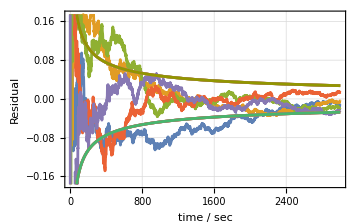
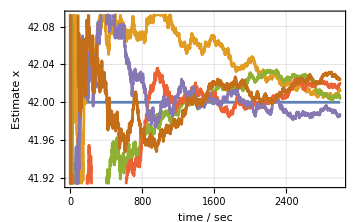
-Graphics-
-Graphics-
% position resids < σ (Expect >= 68) | 76.8211
position resids >= σ | 3478.
position resids < σ | 11527.
average position resid | -0.00383109
theoretical std dev | 0.0273816
std dev of position resids | 0.0694131

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{A_,z_}]:=
Module[{D,K,L,P1,P2,P3,P4,P5,precision=1.*10^-6},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=id[len[P]]-K.A;
P1=L.P;P2=(L.P.Lᵀ+K.Ζ.Kᵀ);P3=(P-K.D.Kᵀ);P4=P.L;P5=P.(Lᵀ);
If[Not[Round[P1,precision]===Round[P2,precision]===
Round[P3,precision]===Round[P4,precision]===Round[P5,precision]],
Throw[<|"N"->Not[P1==P2==P3==P4==P5],
"P1"->P1,"P2"->P2,"P3"->P3,"P4"->P4,"P5"->P5,
"P1-P2"->(P1-P2),
"P2-P3"->(P2-P3),
"P1-P3"->(P1-P3),
"P1-P4"->(P1-P4),
"P1-P5"->(P1-P5)|>]];
(*Print[<|"N"->Not[P1==P2==P3],"P1"->P1,"P2"->P2,"P3"->P3,"P1-P2"->(P1-P2),"P2-P3"->(P2-P3),"P1-P3"->(P1-P3)|>];*)
(*Print[<|"P1"->P1,"P2"->P2,"P3"->P3,"P1-P2"->(P1-P2),"P2-P3"->(P2-P3),"P1-P3"->(P1-P3)|>];*)
{x+K.(z-A.x),P4}];(* P4 is my arbitrary favorite *)
With[{σz=1.5,fooey$=SeedRandom[43]},
With[{aPrioriState=zero[1,1],
aPrioriCovariance=1000000000id[1],
Ζ=col[{σz^2}]},
experiment1[0,3000,1,aPrioriState,aPrioriCovariance,Ζ,
{dt,t}↦{id[1],col[{RandomVariate[NormalDistribution[42,σz]]}]},
t↦42.,
5]]]
```

Now, a run of 10,000 data, picking P3, the one exposed to nonsensical negative covariance, as we shall see later in practical examples:

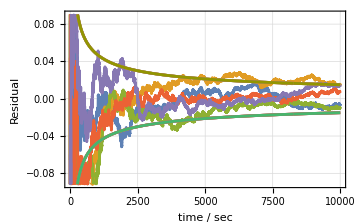
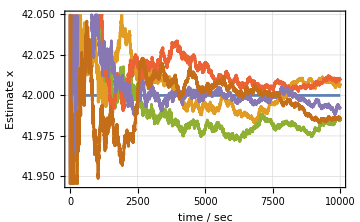
-Graphics-
-Graphics-
% position resids < σ (Expect >= 68) | 83.7876
position resids >= σ | 8107.
position resids < σ | 41898.
average position resid | -0.00561872
theoretical std dev | 0.0149993
std dev of position resids | 0.0393936

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{A_,z_}]:=
Module[{D,K},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
{x+K.(z-A.x),P-K.D.Kᵀ}];
With[{σz=1.5},
With[{aPrioriState=zero[1,1],
aPrioriCovariance=1000000000id[1],
Ζ=col[{σz^2}]},
experiment1[0,10000,1,aPrioriState,aPrioriCovariance,Ζ,
{dt,t}↦{
id[1],
col[{RandomVariate[NormalDistribution[42,σz]]}]},
t↦42.,
5]]]
```

## Part 1: Time-Independent Model

The following is my favorite tiny-test-case. I use it for validating all other Kalman filters.

It is a cubic function of time that depends linearly on four coefficients that we estimate. The ground truth for these coefficients is (-3
9
-4
-5). Faked noisy data and partial derivatives of the model with respect to the coefficients, namely [1,t,t^2,t^3], evaluated at times [-2, -1, 0, 1, 2] constitute the testCase below.

## With Inverse

Inverting D is numerically hazardous and generally contraindicated. We present it, here, because it’s, sadly, most common in publications. We also have yet-another equivalent form for the covariance update, namely P-K.A.P, equally dangerous to P3.

First, define a hard-coded test case. Later, we’ll generate noisy samples from a Gaussian distribution.

```mathematica
ClearAll[testCase];
m/@(testCase={
{{{1,0.,0.,0.}},{-2.28442}},
{{{1,1.,1.,1.}},{-4.83168}},
{{{1,-1.,1.,-1.}},{-10.4601}},
{{{1,-2.,4.,-8.}},{1.40488}},
{{{1,2.,4.,8.}},{-40.8079}}})
```

{({1,0.,0.,0.}
-2.28442),({1,1.,1.,1.}
-4.83168),({1,-1.,1.,-1.}
-10.4601),({1,-2.,4.,-8.}
1.40488),({1,2.,4.,8.}
-40.8079)}

```mathematica
ClearAll[kalman];
kalman[Z_][{x_,P_},{A_,z_}]:=
Module[{D,K},
D=Z+A.P.Aᵀ;
K=P.Aᵀ.Inverse[D];
{x+K.(z-A.x),P-K.A.P}];
```

```mathematica
m@(m/@#&/@
Chop[FoldList[
kalman[IdentityMatrix[1]],
{col[{0,0,0,0}],
id[4]*1000.0},
testCase]])
```

((0
0
0
0) | (1000. | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28214
0
0
0) | (0.999001 | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28299
-0.849281
-0.849281
-0.849281) | (0.998669 | -0.332779 | -0.332779 | -0.332779
-0.332779 | 666.889 | -333.111 | -333.111
-0.332779 | -333.111 | 666.889 | -333.111
-0.332779 | -333.111 | -333.111 | 666.889)
(-2.28749
1.40675
-5.35572
1.40675) | (0.998004 | 0 | -0.997506 | 0
0 | 500.125 | 0 | -499.875
-0.997506 | 0 | 1.49676 | 0
0 | -499.875 | 0 | 500.125)
(-2.29399
7.92347
-5.34488
-5.1154) | (0.997508 | 0.49762 | -0.996678 | -0.498035
0.49762 | 1.3855 | -0.829836 | -0.719881
-0.996678 | -0.829836 | 1.49538 | 0.830528
-0.498035 | -0.719881 | 0.830528 | 0.553787)
(-2.97423
7.2624
-4.21051
-4.45378) | (0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839))

## No Inverse

We get rid of the inverse, pro forma, via Mathematica’s built-in LinearSolve, though inverse does not cause numerical issues in this tiny example, it can and often does, causing failure in the field:

```mathematica
ClearAll[noInverseKalman];
noInverseKalman[Z_][{x_,P_},{A_,z_}]:=
Module[{PAT,D,KRes,KAP},
PAT=P.Aᵀ;
D=Z+A.PAT;
KRes=PAT.LinearSolve[D,z-A.x];
KAP=PAT.LinearSolve[D,A.P];
Chop@{x+KRes,P-KAP}];
```

```mathematica
m@(m/@#&/@
Chop[FoldList[
noInverseKalman[IdentityMatrix[1]],
{col[{0,0,0,0}],
id[4]*1000.0},
testCase]])
```

((0
0
0
0) | (1000. | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28214
0
0
0) | (0.999001 | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28299
-0.849281
-0.849281
-0.849281) | (0.998669 | -0.332779 | -0.332779 | -0.332779
-0.332779 | 666.889 | -333.111 | -333.111
-0.332779 | -333.111 | 666.889 | -333.111
-0.332779 | -333.111 | -333.111 | 666.889)
(-2.28749
1.40675
-5.35572
1.40675) | (0.998004 | 0 | -0.997506 | 0
0 | 500.125 | 0 | -499.875
-0.997506 | 0 | 1.49676 | 0
0 | -499.875 | 0 | 500.125)
(-2.29399
7.92347
-5.34488
-5.1154) | (0.997508 | 0.49762 | -0.996678 | -0.498035
0.49762 | 1.3855 | -0.829836 | -0.719881
-0.996678 | -0.829836 | 1.49538 | 0.830528
-0.498035 | -0.719881 | 0.830528 | 0.553787)
(-2.97423
7.2624
-4.21051
-4.45378) | (0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839))

## Insensitivity to A-Priori State Covariance

Reminder that

```mathematica
groundTruth=({{-3}, {9}, {-4}, {-5}})
```

In the displays, position refers to the first coefficient, with ground truth -3, and speed refers to the second coefficient, with ground truth 9. These labels look forward to tracking examples with physical position and speed states of the system. The display uses the hard-coded test case we wrote out above.

```mathematica
m/@Chop[Fold[kalman[id@1],{col[{0,0,0,0}],id[4]*1000.0},testCase]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

```mathematica
m/@Chop[Fold[kalman[id@1],{col[{0,0,0,0}],id[4]*1000000.0},testCase]]
```

{(-2.97507
7.27
-4.21039
-4.4558),(0.485714 | 0 | -0.142857 | 0
0 | 0.902777 | 1.17883×10^-10 | -0.236111
-0.142857 | 0 | 0.0714285 | 0
0 | -0.236111 | 0 | 0.0694444)}

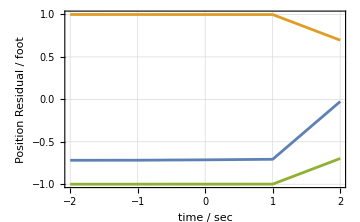
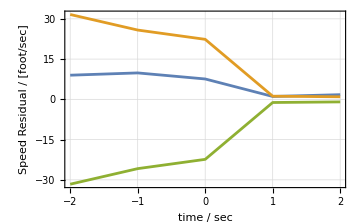
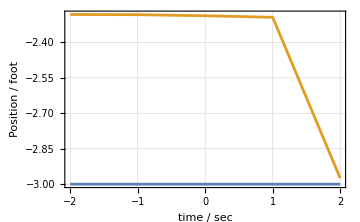
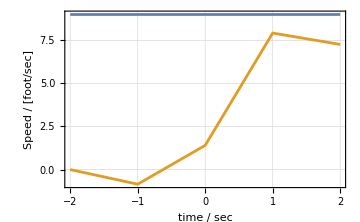
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 100.
position resids >= σ | 0.
position resids < σ | 5.
average position resid | -0.575834
theoretical std dev | 0.696748
std dev of position resids | 0.307529 | % speed resids < σ (Expect >= 68) | 80.
speed resids >= σ | 1.
speed resids < σ | 4.
average speed resid | 5.85133
theoretical std dev | 0.949688
std dev of speed resids | 4.14287

```mathematica
With[{σz=1.},
With[{aPrioriState=zero[4,1],
aPrioriCovariance=1000id[4],
Ζ=col[{σz^2}]},
experiment[-2,2,1,aPrioriState,aPrioriCovariance,Ζ,
{dt,t}↦{testCase⟦3+t,1⟧,testCase⟦3+t,2⟧},
t↦groundTruth⟦1,1⟧,
t↦groundTruth⟦2,1⟧,
1]]]
```

Do an experiment with a randomized version of the same model instead of the hard-coded test case.

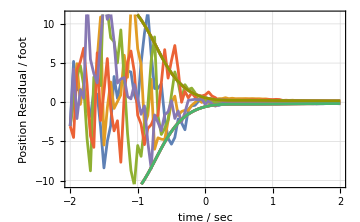
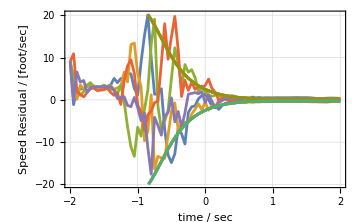
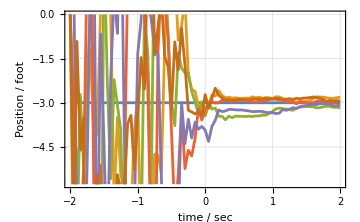
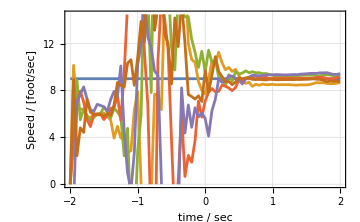
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 82.2222
position resids >= σ | 72.
position resids < σ | 333.
average position resid | 0.452444
theoretical std dev | 0.166685
std dev of position resids | 3.22507 | % speed resids < σ (Expect >= 68) | 74.8148
speed resids >= σ | 102.
speed resids < σ | 303.
average speed resid | 0.638513
theoretical std dev | 0.23773
std dev of speed resids | 4.57455

```mathematica
With[{σz=1.},
With[{aPrioriState=zero[4,1],
aPrioriCovariance=1000[4],
Ζ=col[{σz^2}]},
Module[{A},
A[t_]:=row[{1,t,t^2,t^3}];
experiment[-2,2,.05,zero[4,1],1000id[4],1.0,
{dt,t}↦{A[t],scalar[A[t].groundTruth+gen[Ζ]]},
t↦groundTruth⟦1,1⟧,
t↦groundTruth⟦2,1⟧,
5]]]]
```

## Part 2: Tracking (Time-Dependent Model)

Process-Noise Matrix

Process noise enters the last state, and with a constant standard deviation. Integrate the process-noise covariance matrix over a discrete time interval and over a particular model of system dynamics to add its effects to the filter.

```mathematica
ClearAll[Q,Φ,σx,t];
Q=({{0, 0, 0}, {0, 0, 0}, {0, 0, ξ^2}});
Φ[t_]:=({{1, t, t^2/2}, {0, 1, t}, {0, 0, 1}});
Integrate[Φ[t].Q.Transpose[Φ[t]],{t,0,δt}]//m
```

((δt^5 ξ^2)/20 | (δt^4 ξ^2)/8 | (δt^3 ξ^2)/6
(δt^4 ξ^2)/8 | (δt^3 ξ^2)/3 | (δt^2 ξ^2)/2
(δt^3 ξ^2)/6 | (δt^2 ξ^2)/2 | δt ξ^2)

As A Fold

kalman is the Kalman filter with time-dependent dynamical process.

At the bottom, we validate that kalman degenerates to the original static case.

Ξ is the integrated process-noise matrix. It depend on time and on the size of the time step.

Φ is the integral of the system-dynamics matrix F; more precisely, Φ is Exp[F t].

Γ is the time-step integral of system response G propagated by Φ.

Ξ, Φ, Γ, and u may all depend on time and on the size of the time step.

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
(* demonstrate that the filter degenerates to the earlier form given a time-independent model *)
m/@
Chop[
With[{
Ξ=zero[4],Ζ=id[1],
Φ=id[4],Γ=zero[4,1],u=zero[1]},
Fold[
kalman[Ζ],
{col[{0,0,0,0}],
id[4]*1000.0},
{Ξ,Φ,Γ,u}⊕#&/@testCase
]]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
(*If[Not[PT1==PT2==PT3],Throw[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>]];*)
(*Print[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->Chop@(PT1-PT2),"PT2-PT3"->Chop@(PT2-PT3),"PT1-PT3"->Chop@(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"D"->D|>];*)
{x2+K.(z-A.x2),PT3}];
(* demonstrate that the filter degenerates to the earlier form given a time-independent model *)
m/@
Chop[
With[{
Ξ=zero[4],Ζ=id[1],
Φ=id[4],Γ=zero[4,1],u=zero[1]},
Fold[
kalman[Ζ],
{col[{0,0,0,0}],
id[4]*1000.0},
{Ξ,Φ,Γ,u}⊕#&/@testCase
]]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

Track a Falling Object

Reproduce three-state and two-state examples from Zarchan and Musoff, Fundamentals of Kalman Filtering, A Practical Approach, Ch. 4, track a falling object, no air drag, but with various forms for the covariance update, those with potentially low numerical risk and those with potentially high numerical risk. For these examples, the risk has no effect on the outcome, at least visually. We shall soon see cases where there is visible difference, mandating a low-risk form. The computational speed of these various forms is not considered, here, only the potential risk of catastrophic cancelation leading to negative covariance estimates.

## Three-State Falling Object

There are three states: the position x, velocity ẋ, acceleration ẍ. The observations z directly measure the position state.

State-space form:

```mathematica
ClearAll[x,xd,xdd,Ψ,u,F,Φ,Ξc,Ξ,G,Γ,A];
u[t_]:=col[{g}];
Ψ=({{x}, {xd}, {xdd}});F=({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}});G=({{0}, {0}, {1}});
Φ[dt_]:=({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}});Γ[dt_]:=({{dt^2/2}, {dt}, {1}});
Ξc=({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
Ξ[dt_]:=({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}});
A[t_]:=({{1, 0, 0}});
```

Track with the risky P3 = Ξ+Φ.P.Φᵀ - K.D.Kᵀ.

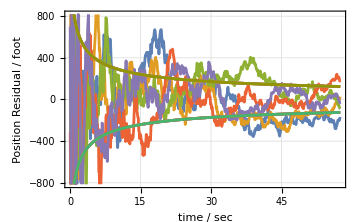
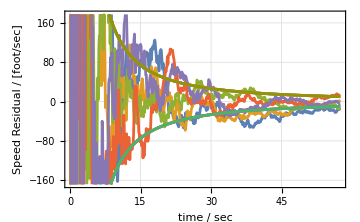
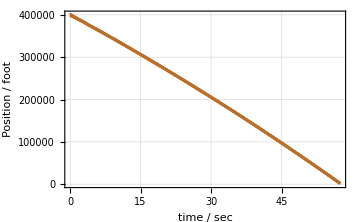
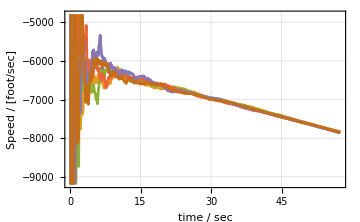
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 64.3056
position resids >= σ | 1028.
position resids < σ | 1852.
average position resid | 5.99396
theoretical std dev | 124.568
std dev of position resids | 248.361 | % speed resids < σ (Expect >= 68) | 67.4306
speed resids >= σ | 938.
speed resids < σ | 1942.
average speed resid | -43.8473
theoretical std dev | 10.0073
std dev of speed resids | 2395.91

```mathematica
With[{x0=400000.,v0=-6000.,a0=-32.2,σz=1000.,σx=0},
With[{aPrioriState=zero[3,1](*col[{x0,v0,a0}]*),
aPrioriCovariance=1000000000000id[3],
Ζ=col[{σz^2}]},
SeedRandom[42];
experiment[0,57.5,0.1,aPrioriState,aPrioriCovariance,Ζ,
{dt,t}↦
{σx^2({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}}), (* process noise *)
({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}, {1}}), (* system response *)
zero[1], (* external force *)
({{1, 0, 0}}), (* observation partials *)
col[{x0+v0 t+(a0 t^2)/2}]+gen[Ζ]}, (* observation fake *)
t↦x0+v0 t+a0 t^2/2, (* true position *)
t↦v0+a0 t (* true speed *),5]]]
```

Track with the potentially less risky PT1=(id[len[P]]-K.A).(Ξ+Φ.P.Φᵀ).

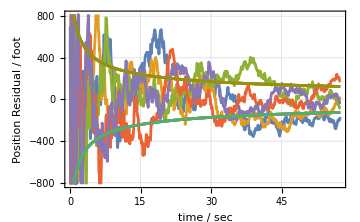
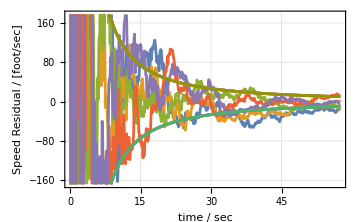
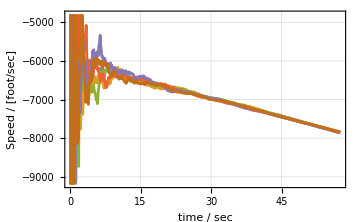
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 64.3056
position resids >= σ | 1028.
position resids < σ | 1852.
average position resid | 5.99389
theoretical std dev | 124.567
std dev of position resids | 248.361 | % speed resids < σ (Expect >= 68) | 67.4306
speed resids >= σ | 938.
speed resids < σ | 1942.
average speed resid | -43.8473
theoretical std dev | 10.0072
std dev of speed resids | 2395.91

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
(*If[Not[PT1==PT2==PT3],Throw[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>]];*)
(*Print[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->Chop@(PT1-PT2),"PT2-PT3"->Chop@(PT2-PT3),"PT1-PT3"->Chop@(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"D"->D|>];*)
{x2+K.(z-A.x2),PT1}];
With[{x0=400000.,v0=-6000.,a0=-32.2,σz=1000.,σx=0},
With[{aPrioriState=zero[3,1](*col[{x0,v0,a0}]*),
aPrioriCovariance=1000000000000id[3],
Ζ=col[{σz^2}]},
SeedRandom[42];
experiment[0,57.5,0.1,aPrioriState,aPrioriCovariance,Ζ,
{dt,t}↦
{σx^2({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}}), (* process noise *)
({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}, {1}}), (* system response *)
zero[1], (* external force *)
({{1, 0, 0}}), (* observation partials *)
col[{x0+v0 t+(a0 t^2)/2}]+gen[Ζ]}, (* observation fake *)
t↦x0+v0 t+a0 t^2/2, (* true position *)
t↦v0+a0 t (* true speed *),5]]]
```

The results are visually indistinguishable.

## Two-State Falling Object

Track a two-state system with a potentially low-risk PT1=(id[len[P]]-K.A).(Ξ+Φ.P.Φᵀ).

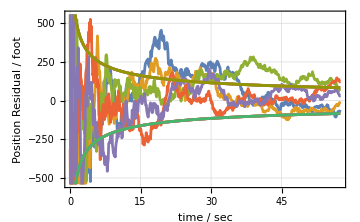
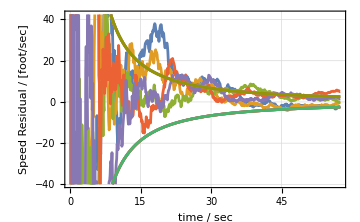
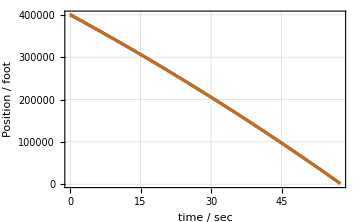
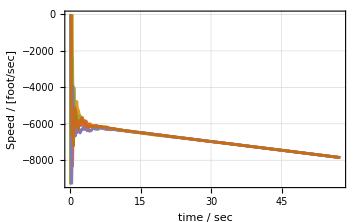
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 67.5694
position resids >= σ | 934.
position resids < σ | 1946.
average position resid | 23.3763
theoretical std dev | 83.2249
std dev of position resids | 176.477 | % speed resids < σ (Expect >= 68) | 71.9792
speed resids >= σ | 807.
speed resids < σ | 2073.
average speed resid | -110.218
theoretical std dev | 2.50586
std dev of speed resids | 1982.39

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
(*If[Not[PT1==PT2==PT3],Throw[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>]];*)
(*Print[<|"N"->Not[PT1==PT2==PT3],"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->(PT1-PT2),"PT2-PT3"->(PT2-PT3),"PT1-PT3"->(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"PT1-PT2"->Chop@(PT1-PT2),"PT2-PT3"->Chop@(PT2-PT3),"PT1-PT3"->Chop@(PT1-PT3)|>];*)
(*Print[<|"PT1"->PT1,"PT2"->PT2,"PT3"->PT3,"D"->D|>];*)
{x2+K.(z-A.x2),PT1}];
With[{x0=400000,v0=-6000,g=-32.2,σz=1000.,σx=0.},
With[{aPrioriState=zero[2,1],
aPrioriCovariance=1000000000000id[2],
Ζ=col[{σz^2}]},
SeedRandom[42];
experiment[0,57.5,0.1,aPrioriState,aPrioriCovariance,
Ζ, (* observation-noise covariance *)
{dt,t}↦
{σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),(* process noise *)
({{1, dt}, {0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}}), (* system response *)
col[{g}], (* external force *)
({{1, 0}}), (* observation partials *)
col[{x0+v0 t+g t^2/2}]+gen[Ζ] (* observation fake *)},
t↦x0+v0 t+g t^2/2, (* true position *)
t↦v0+g t (* true speed *),5]]]
```

Now with a potentially low-risk PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ), where L=id[len[P]]-K.A.

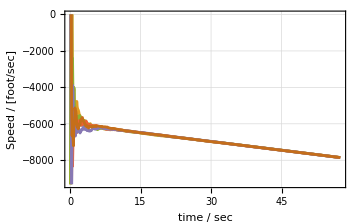
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 67.5694
position resids >= σ | 934.
position resids < σ | 1946.
average position resid | 23.3763
theoretical std dev | 83.2249
std dev of position resids | 176.477 | % speed resids < σ (Expect >= 68) | 71.9792
speed resids >= σ | 807.
speed resids < σ | 2073.
average speed resid | -110.218
theoretical std dev | 2.50586
std dev of speed resids | 1982.39

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
{x2+K.(z-A.x2),PT2}];
With[{x0=400000,v0=-6000,g=-32.2,σz=1000.,σx=0.},
With[{aPrioriState=zero[2,1],
aPrioriCovariance=1000000000000id[2],
Ζ=col[{σz^2}]},
SeedRandom[42];
experiment[0,57.5,0.1,aPrioriState,aPrioriCovariance,
Ζ, (* observation-noise covariance *)
{dt,t}↦
{σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),(* process noise *)
({{1, dt}, {0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}}), (* system response *)
col[{g}], (* external force *)
({{1, 0}}), (* observation partials *)
col[{x0+v0 t+g t^2/2}]+gen[Ζ] (* observation fake *)},
t↦x0+v0 t+g t^2/2, (* true position *)
t↦v0+g t (* true speed *),5]]]
```

Now with a potentially high-risk PT3=Ξ+Φ.P.Φᵀ-K.D.Kᵀ.

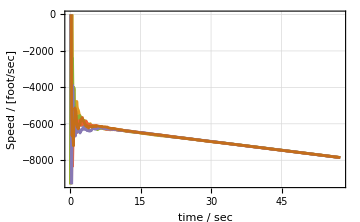
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% position resids < σ (Expect >= 68) | 67.5694
position resids >= σ | 934.
position resids < σ | 1946.
average position resid | 23.3763
theoretical std dev | 83.2249
std dev of position resids | 176.477 | % speed resids < σ (Expect >= 68) | 71.9792
speed resids >= σ | 807.
speed resids < σ | 2073.
average speed resid | -110.218
theoretical std dev | 2.50586
std dev of speed resids | 1982.39

```mathematica
ClearAll[kalman];
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
{x2+K.(z-A.x2),PT3}];
With[{x0=400000,v0=-6000,g=-32.2,σz=1000.,σx=0.},
With[{aPrioriState=zero[2,1],
aPrioriCovariance=1000000000000id[2],
Ζ=col[{σz^2}]},
SeedRandom[42];
experiment[0,57.5,0.1,aPrioriState,aPrioriCovariance,
Ζ, (* observation-noise covariance *)
{dt,t}↦
{σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),(* process noise *)
({{1, dt}, {0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}}), (* system response *)
col[{g}], (* external force *)
({{1, 0}}), (* observation partials *)
col[{x0+v0 t+g t^2/2}]+gen[Ζ] (* observation fake *)},
t↦x0+v0 t+g t^2/2, (* true position *)
t↦v0+g t (* true speed *),5]]]
```

## Part 1: Time-Dependent Observation Noise (TDZ)

## KalmanTDZ

TODO: Limitation: scalar observations only.

```mathematica
(* make a foldable kalman filter that takes Zeta as an extra input *)
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
(*Print[<|"D"->D,"K"->K,"x"->x,"Ζ"->Ζ,"P"->P,"xn"->x2+K.(z-A.x2),"Pn"->P2-K.D.K^ᵀ|>];*)
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
(* demonstrate that the filter degenerates to the earlier form given a time-independent model *)
m/@
Chop[
With[{
Ξ=zero[4],Ζ=id[1],
Φ=id[4],Γ=zero[4,1],u=zero[1]},
Fold[
kalmanTDZ,
{col[{0,0,0,0}],
id[4]*1000.0},
{Ζ,Ξ,Φ,Γ,u}⊕#&/@testCase
]]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

## Three-State Accelerometer (TIS, TDZ)

Time-Independent State, Time-Dependent Observation Noise

### sqrt

Sow values if sqrt is attempted on a negative variance.

```mathematica
ClearAll[sqrt];
SetAttributes[sqrt,Listable];
sqrt[z_]:=With[{zc=Identity[z]},
If[zc<0,Sow[<|"z"->z,"zc"->zc|>,"sqrt"];Sqrt[zc],Sqrt[zc]]];
```

### stir

Move labels around in a labels packet. TODO: This can probably be removed, but it make labels packet easier if we apply stir to its result. This is a minor annoyance at best. Don’t bikeshed too much.

```mathematica
ClearAll[stir];
stir[l_]:=(l⟦1;;len@l;;2⟧)⊕(l⟦2;;len@l;;2⟧)
```

### labelsPacket2

Can handle any number of states.

```mathematica
ClearAll[labelsPacket2,labelsPacket2];
labelsPacket2[_,{}]:={};
labelsPacket2[
j:{indNym_String,indUnits_String},{{nym_String,units_String},more___}]:=
Module[{brk,fst},
brk[q_String]:=" / ["<>q<>"]";
fst[q_String]:=nym<>q<>brk@units;
With[{ind=indNym<>brk@indUnits,
res=" Residual",resvs=" Residuals vs. ",
trtvs=" Truth and Estimates vs. "},
{{{fst[res],""},{ind,nym<>resvs<>indNym}},
{{fst[""],""},{ind,nym<>trtvs<>indNym}}}⊕
labelsPacket2[j,{more}]
]];
```

## ExperimentTDZ

TODO: Poorly named; this is a full replacement for experiment.

```mathematica
ClearAll[experimentTDZ];
experimentTDZ[startTime_,endTime_,timeIncrement_,
aPrioriState_,aPrioriCovariance_,fakeFn_,
nStates_Integer:2,truthFns_List:{Identity,Identity},
labelsPacket_List:stir@labelsPacket2[{"Independent Variable","?dim"},{{"State1","?dim"},{"State2","?dim"}}],
statsLabels_List:{"State1","State2"},iterations_Integer:1]:=
Module[{t,timesIter,times,fakes,estss,
trueStates,estimatedStatess,residualStatess,
stddevStatess,theoStateVarss,statsStates,styler},
styler=myStyle/@#&;
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
trueStates=Table[truthFns⟦n⟧[t],{n,nStates},Evaluate@timesIter];
fakes[]:=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
estss=Table[
FoldList[kalmanTDZ,{aPrioriState,aPrioriCovariance},fakes[]],
iterations];
(* starts at 2;; to skip the a-priori *)
estimatedStatess=Table[estss⟦;;,2;;,1,n,1⟧,{n,nStates}];
residualStatess=Table[
Identity[trueStates⟦n⟧-#&/@estimatedStatess⟦n⟧],
{n,nStates}];
stddevStatess=Table[sqrt@estss⟦(;;),(2;;),2,n,n⟧,{n,nStates}];
theoStateVarss=Table[Last[estss⟦1⟧]⟦2,n,n⟧,{n,nStates}];
statsStates=Table[
stats[statsLabels⟦n⟧,
f1@residualStatess⟦n⟧,
f1@stddevStatess⟦n⟧,
theoStateVarss⟦n⟧],{n,nStates}];
Grid@{
Table[
ListLinePlot[(withTimes[times,#]&/@residualStatess⟦n⟧)⊕
(withTimes[times,#]&/@stddevStatess⟦n⟧)⊕
(withTimes[times,#]&/@-stddevStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
Table[
ListLinePlot[{withTimes[times,trueStates⟦n⟧]}⊕
(withTimes[times,#]&/@estimatedStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n+nStates⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
statsStates}];
```

## ExperimentTDZ with Three-State Accelerometer

### With P ← L.P.Lᵀ+K.Z.Kᵀ

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Kᵀ;
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P3(*P2-K.D.K^ᵀ*)}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Indpendent variable is θ.

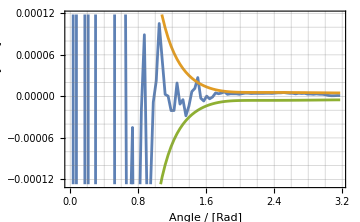
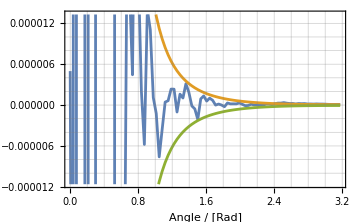
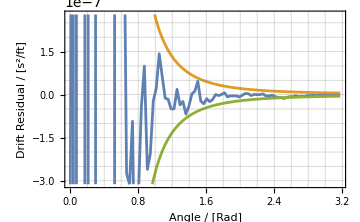
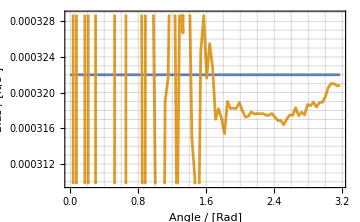
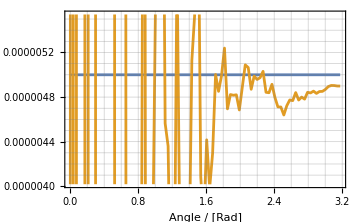
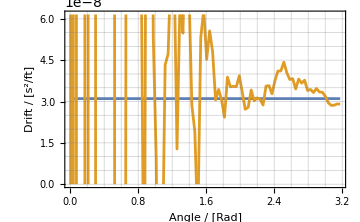
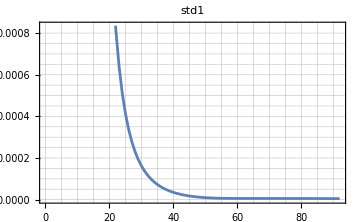
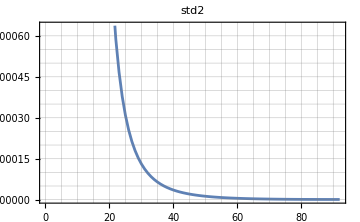
{{{{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 83.6957
Bias resids >= σ | 4.
Bias resids < σ | 77.
average Bias resid | 0.00358082
theoretical std dev | 5.02418×10^-6
std dev of Bias resids | 0.0923306 | % Scale resids < σ (Expect >= 68) | 60.8696
Scale resids >= σ | 25.
Scale resids < σ | 56.
average Scale resid | -0.000193406
theoretical std dev | 6.66051×10^-8
std dev of Scale resids | 0.00597229 | % Drift resids < σ (Expect >= 68) | 83.6957
Drift resids >= σ | 4.
Drift resids < σ | 77.
average Drift resid | 2.51554×10^-6
theoretical std dev | 5.79413×10^-9
std dev of Drift resids | 0.0000968455,{-Graphics-}},{-Graphics-}},{-Graphics-}}}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦
With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],
{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

### With P ← L.P

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Transpose[K];
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P1(*P2-K.D.Kᵀ*)}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Indpendent variable is θ.

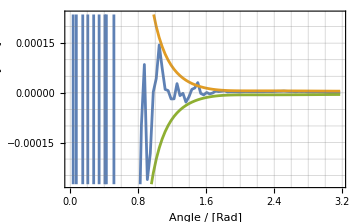
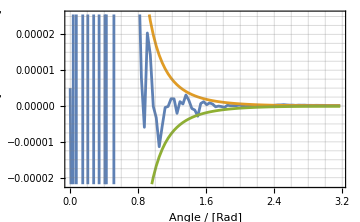
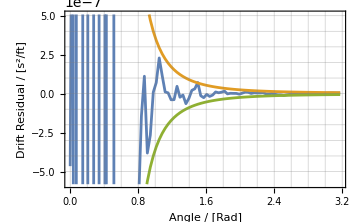
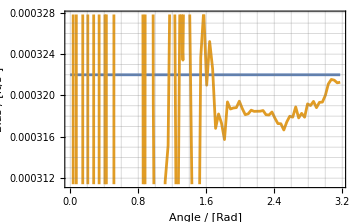
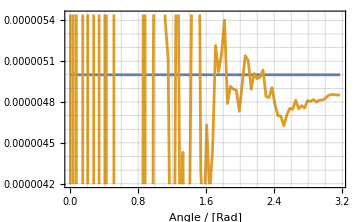
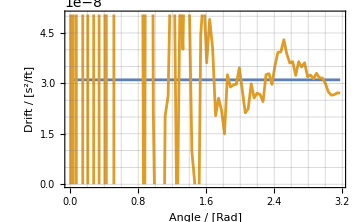
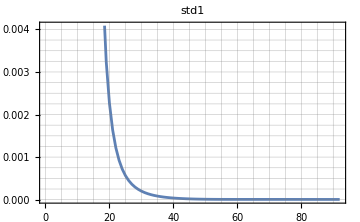
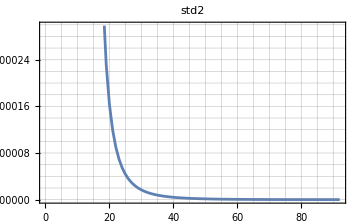
{{{{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 86.9565
Bias resids >= σ | 7.
Bias resids < σ | 80.
average Bias resid | 0.0113483
theoretical std dev | 5.08884×10^-6
std dev of Bias resids | 0.114917 | % Scale resids < σ (Expect >= 68) | 61.9565
Scale resids >= σ | 30.
Scale resids < σ | 57.
average Scale resid | -0.000714109
theoretical std dev | 9.08003×10^-8
std dev of Scale resids | 0.00717694 | % Drift resids < σ (Expect >= 68) | 85.8696
Drift resids >= σ | 8.
Drift resids < σ | 79.
average Drift resid | 0.0000112456
theoretical std dev | 6.39081×10^-9
std dev of Drift resids | 0.000112081,{-Graphics-}},{-Graphics-}},{-Graphics-}}}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},
{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

### With P ← P-K.D.Kᵀ

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Kᵀ;
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P4(*P2-K.D.K^ᵀ*)}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Indpendent variable is θ.

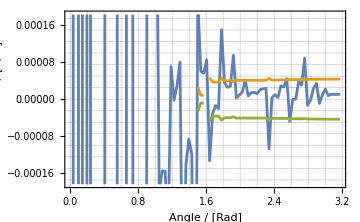
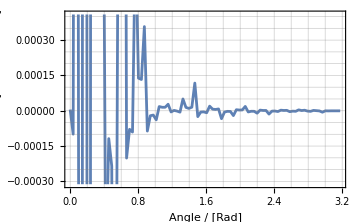
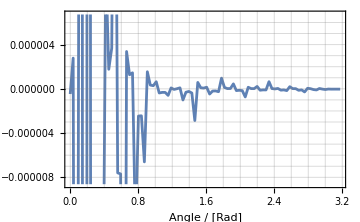
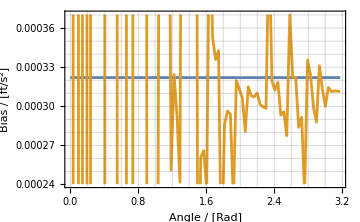
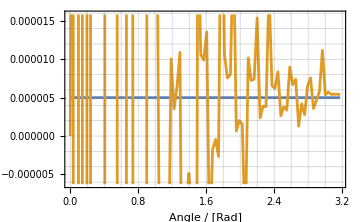
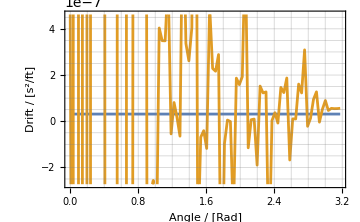
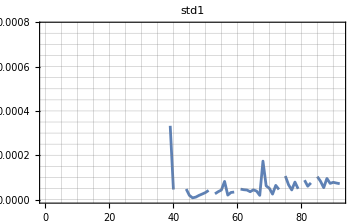
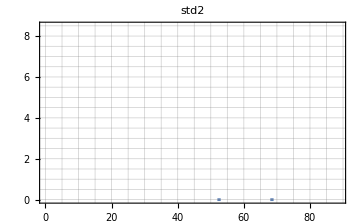
{{{{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 48.913
Bias resids >= σ | 13.
Bias resids < σ | 45.
average Bias resid | -0.00498231
theoretical std dev | 0.0000434082
std dev of Bias resids | 0.0729717 | % Scale resids < σ (Expect >= 68) | 7.6087
Scale resids >= σ | 3.
Scale resids < σ | 7.
average Scale resid | 0.000320187
theoretical std dev | 0.+2.6977×10^-6 ⅈ
std dev of Scale resids | 0.00458956 | % Drift resids < σ (Expect >= 68) | 7.6087
Drift resids >= σ | 4.
Drift resids < σ | 7.
average Drift resid | -5.16615×10^-6
theoretical std dev | 0.+7.28827×10^-8 ⅈ
std dev of Drift resids | 0.0000721718,{-Graphics-}},{-Graphics-}},{-Graphics-}}}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},
{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

## Comparison with Zarchan & Musoff’s Three-State Accelerometer

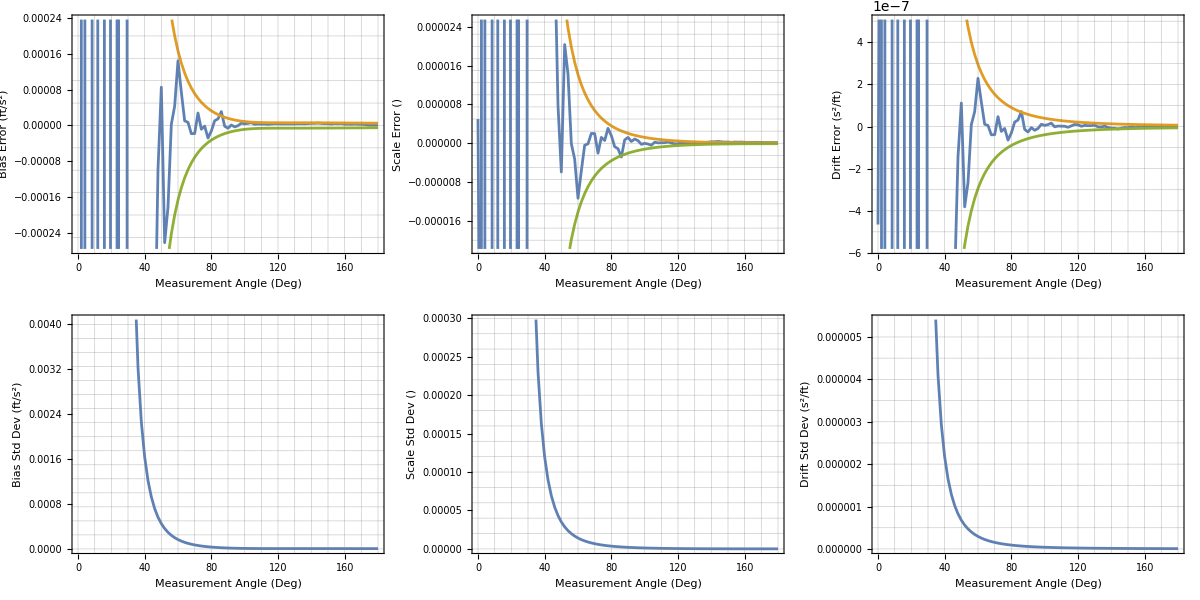
{-Graphics-,{316075.,19609.5,20153.4,0.+34750.3 ⅈ,3096.18,0.+943.512 ⅈ,111.79,168.657,5.05559,0.+3.00108 ⅈ,0.588137,0.+0.0330254 ⅈ,0.+0.010045 ⅈ,0.00594021,0.00188567,0.000929563,0.000537759,0.000341305,0.000230592,0.000163069,0.000119432,0.0000899436,0.0000692955,0.0000544077,0.0000434091,0.0000351136,0.0000287444,0.0000237773,0.0000198506,0.0000167087,0.0000141673,0.0000120918,0.0000103818,8.96171×10^-6,7.77381×10^-6,6.77353×10^-6,5.9261×10^-6,5.20414×10^-6,4.58587×10^-6,4.05386×10^-6,3.59403×10^-6,3.19493×10^-6,2.84721×10^-6,2.54316×10^-6,2.27641×10^-6,2.04164×10^-6,1.8344×10^-6,1.65096×10^-6,1.48817×10^-6,1.34336×10^-6,1.21425×10^-6,1.0989×10^-6,9.95628×10^-7,9.03015×10^-7,8.19816×10^-7,7.44959×10^-7,6.77515×10^-7,6.16673×10^-7,5.61725×10^-7,5.12053×10^-7,4.67117×10^-7,4.26439×10^-7,3.89601×10^-7,3.56234×10^-7,3.26012×10^-7,2.98647×10^-7,2.73886×10^-7,2.515×10^-7,2.31291×10^-7,2.13078×10^-7,1.96703×10^-7,1.82021×10^-7,1.68902×10^-7,1.57228×10^-7,1.4689×10^-7,1.37784×10^-7,1.29815×10^-7,1.22888×10^-7,1.16915×10^-7,1.11806×10^-7,1.07476×10^-7,1.03841×10^-7,1.0082×10^-7,9.83365×10^-8,9.6318×10^-8,9.46973×10^-8,9.34134×10^-8,9.2412×10^-8,9.16466×10^-8,9.10857×10^-8,9.08009×10^-8}}

```mathematica
Module[{
order=3,
bias=.00001 * 32.2,
sf=.000005,
xk=.000001/32.2,
sigth=.000001,
g=32.2,
biash=0,
sfh=0,
xkh=0,
signoise=.000001,
s=0,
q=0IdentityMatrix[3],
phi=IdentityMatrix[3],
idnp=IdentityMatrix[3],
p=99999999999IdentityMatrix[3],
ppri,
count=0,
thetdeg,thet,thetnoise,thets,hmat,r,m,k,z,res,sp11,sp22,sp33,sp11p,sp22p,sp33p,biaserr,sferr,xkerr,actnoise,sigr,sigrp,
arraythetdeg,arraybias,arraymhmatt,arrayk11,arrayz,arrayres,arraybiash,arraysf,arraysfh,arrayxk,arrayxkh,arraybiaserr,arraysp11,arraysp11p,arraysferr,arraysp22,arraysp22p,arrayxkerr,arraysp33,arraysp33p,arrayactnoise,arraysigr,arraysigrp},
SeedRandom[42];
{arraythetdeg,arraybias,arraymhmatt,arrayk11,arrayz,arrayres,arraybiash,arraysf,arraysfh,arrayxk,arrayxkh,arraybiaserr,arraysp11,arraysp11p,arraysferr,arraysp22,arraysp22p,arrayxkerr,arraysp33,arraysp33p,arrayactnoise,arraysigr,arraysigrp}=
Reap[For[
thetdeg=0,thetdeg≤180.,thetdeg+=2.,
Sow[thetdeg,"thetdeg"];
Sow[bias,"bias"];
thet=thetdeg*(1.0°)(*/57.3*);
thetnoise=randn@signoise;
thets=thet+thetnoise;
hmat={{1,g Cos[thets],(g Cos[thets])^2}};
r=(g Sin[thets]sigth)^2 IdentityMatrix[1];
m=phi.p.(Transpose[phi])+q;
k=m.(Transpose[hmat]).Inverse[hmat.m.(Transpose[hmat])+r];
Sow[(m.(Transpose[hmat]))⟦1,1⟧,"hmatt"];
Sow[k⟦1,1⟧,"k11"];
ppri=p;
p=(idnp-k.hmat).m;
(*Print[<|"P"->p|>];*)
Sow[z=bias+sf g Cos[thets]+xk (g Cos[thets])^2-g Cos[thet]+g Cos[thets],"z"];
Sow[res=z-biash-sfh g Cos[thets]-xkh(g Cos[thets])^2,"res"];
Sow[biash=biash+k⟦1,1⟧res,"biash"];
Sow[sf,"sf"];
Sow[sfh=sfh+k⟦2,1⟧res,"sfh"];
Sow[xk,"xk"];
Sow[xkh=xkh+k⟦3,1⟧res,"xkh"];
Sow[biaserr=bias-biash,"biaserr"];
Sow[sp11=Sqrt[p⟦1,1⟧],"sp11"];
Sow[sp11p=-sp11,"sp11p"];
Sow[sferr=sf-sfh,"sferr"];
Sow[sp22=Sqrt[p⟦2,2⟧],"sp22"];
Sow[sp22p=-sp22,"sp22p"];
Sow[xkerr=xk-xkh,"xkerr"];
Sow[sp33=Sqrt[p⟦3,3⟧],"sp33"];
Sow[sp33p=-sp33,"sp33p"];
Sow[actnoise=g Cos[thets]-g Cos[thet],"actnoise"];
Sow[sigr=Sqrt[r⟦1,1⟧],"sigr"];
Sow[sigrp=-sigr,"sigrp"];
count=count+1;
]]⟦2⟧;
{Grid[
{{ListLinePlot[{Transpose[{arraythetdeg,arraybiaserr}],Transpose[{arraythetdeg,arraysp11}],Transpose[{arraythetdeg,arraysp11p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Bias Error (ft/s^2)",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysferr}],Transpose[{arraythetdeg,arraysp22}],Transpose[{arraythetdeg,arraysp22p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Scale Error ()",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arrayxkerr}],Transpose[{arraythetdeg,arraysp33}],Transpose[{arraythetdeg,arraysp33p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Drift Error (s^2/ft)",""},{"Measurement Angle (Deg)",""}}]},
{ListLinePlot[{Transpose[{arraythetdeg,arraysp11}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Bias Std Dev (ft/s^2)",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysp22}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Scale Std Dev ()",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysp33}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Drift Std Dev (s^2/ft)",""},{"Measurement Angle (Deg)",""}}]
}}],
arraysp22}]
```

### ExperimentTDZ Estimating the Mean

Reminder of new experiment signature; closes over kalmanTDZ , which takes {Ζ, A, z}

experimentTDZ[t_0,t_1,δt,
x̃,P̃,{δt,t}↦ {Ζ,A,z},
nStates:2,truthFns:{Ident,Ident},
labelsPacket:"a basic default; don't forget to stir",
statsLabels_List:{"state1","state2"},iterations:1]

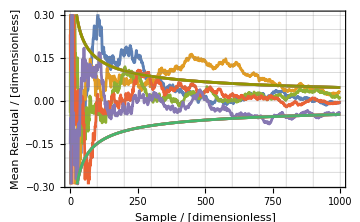
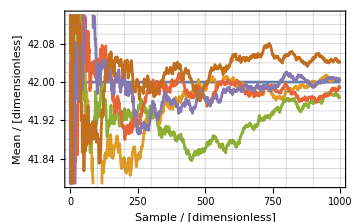
-Graphics-
-Graphics-
% Mean resids < σ (Expect >= 68) | 81.3986
Mean resids >= σ | 931.
Mean resids < σ | 4074.
average Mean resid | 0.019131
theoretical std dev | 0.0474105
std dev of Mean resids | 0.114848

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
{x+K.(z-A.x),L.P}];
With[{σz=1.5},
With[{aPrioriState=zero[1,1],
aPrioriCovariance=1000000000id[1],
Ζ=col[{σz^2}]},
experimentTDZ[0,1000,1,aPrioriState,aPrioriCovariance,
{dt,t}↦{
Ζ,
id[1],
col[{RandomVariate[NormalDistribution[42,σz]]}]},
1,
{t↦42.},
stir@labelsPacket2[{"Sample","dimensionless"},
{{"Mean","dimensionless"}}],
{"Mean"},
5]]]
```

### ExperimentTDZ Estimating the Three-State Falling Object with No Drag

Reminder of new experiment signature; closes over kalmanTDZ , which takes {Ζ, A, z}

experimentTDZ[t_0,t_1,δt,
x̃,P̃,{δt,t}↦ {Ζ,Ξ,Φ,Γ,u,A,z},
nStates:2,truthFns:{Ident,Ident},
labelsPacket:"a basic default; don't forget to stir",
statsLabels_List:{"state1","state2"},iterations:1]

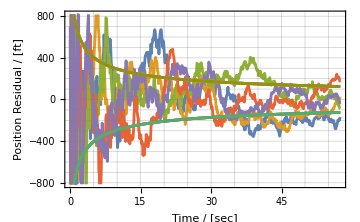
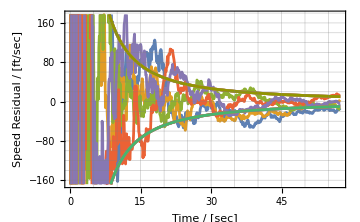
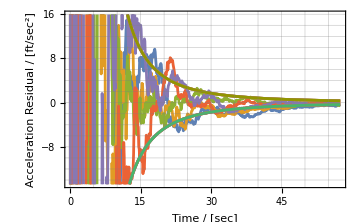
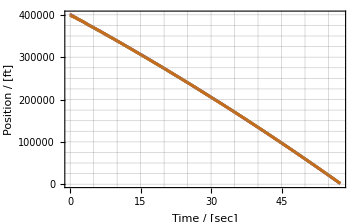
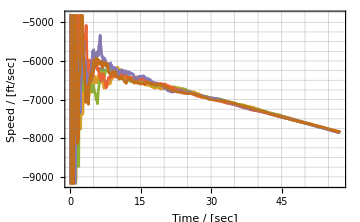
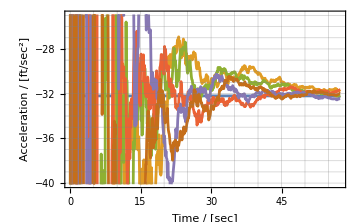
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Position resids < σ (Expect >= 68) | 64.3056
Position resids >= σ | 1028.
Position resids < σ | 1852.
average Position resid | 5.99396
theoretical std dev | 124.568
std dev of Position resids | 248.361 | % Speed resids < σ (Expect >= 68) | 67.4306
Speed resids >= σ | 938.
Speed resids < σ | 1942.
average Speed resid | -43.8473
theoretical std dev | 10.0073
std dev of Speed resids | 2395.91 | % Acceleration resids < σ (Expect >= 68) | 67.9167
Acceleration resids >= σ | 924.
Acceleration resids < σ | 1956.
average Acceleration resid | 237.605
theoretical std dev | 0.336991
std dev of Acceleration resids | 9656.21

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L,PT1,PT2,PT3},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
L=id[len[P]]-K.A;
PT1=L.P2;PT2=(L.P2.Lᵀ+K.Ζ.Kᵀ);PT3=(P2-K.D.Kᵀ);
{x2+K.(z-A.x2),PT3}];
With[{x0=400000.,v0=-6000.,a0=-32.2,σz=1000.,σx=0,nStates=3},
With[{aPrioriState=zero[nStates,1],
aPrioriCovariance=1000000000000id[nStates],
Ζ=col[{σz^2}]},
SeedRandom[42];
experimentTDZ[0,57.5,0.1,
aPrioriState,aPrioriCovariance,
{dt,t}↦
{Ζ,
σx^2({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}}), (* process noise *)
({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}, {1}}), (* system response *)
zero[1], (* external force *)
({{1, 0, 0}}), (* observation partials *)
col[{x0+v0 t+(a0 t^2)/2}]+gen[Ζ]}, (* observation fake *)
nStates,
{t↦x0+v0 t+a0 t^2/2, (* true position *)
t↦v0+a0 t (* true speed *),
t↦a0 (* true acceleration *)},
stir@labelsPacket2[{"Time","sec"},{{"Position","ft"},{"Speed","ft/sec"},{"Acceleration","ft/sec^2"}}],
{"Position","Speed","Acceleration"},
5(* iterations *)]]]
```

### ExperimentTDZ Estimating the Two-State Falling Object with No Drag

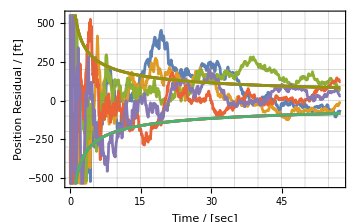
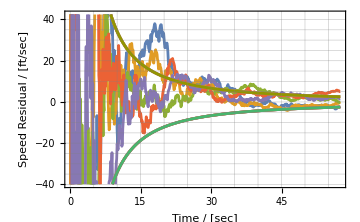
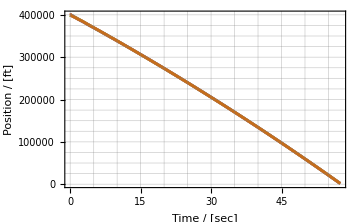
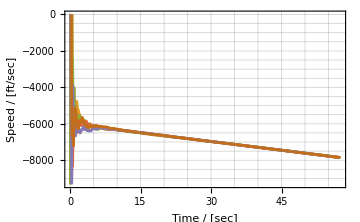
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% Position resids < σ (Expect >= 68) | 67.5694
Position resids >= σ | 934.
Position resids < σ | 1946.
average Position resid | 23.3763
theoretical std dev | 83.2249
std dev of Position resids | 176.477 | % Speed resids < σ (Expect >= 68) | 71.9792
Speed resids >= σ | 807.
Speed resids < σ | 2073.
average Speed resid | -110.218
theoretical std dev | 2.50586
std dev of Speed resids | 1982.39

```mathematica
With[{x0=400000.,v0=-6000.,a0=-32.2,σz=1000.,σx=0,nStates=2},
With[{aPrioriState=zero[nStates,1],
aPrioriCovariance=1000000000000id[nStates],
Ζ=col[{σz^2}]},
SeedRandom[42];
experimentTDZ[0,57.5,0.1,
aPrioriState,aPrioriCovariance,
{dt,t}↦
{Ζ,
σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),(* process noise *)
({{1, dt}, {0, 1}}), (* system dynamics *)
({{dt^2/2}, {dt}}), (* system response *)
col[{a0}], (* external force *)
({{1, 0}}), (* observation partials *)
col[{x0+v0 t+a0 t^2/2}]+gen[Ζ] (* observation fake *)}, (* observation fake *)
nStates,
{t↦x0+v0 t+a0 t^2/2, (* true position *)
t↦v0+a0 t (* true speed *)},
stir@labelsPacket2[{"Time","sec"},{{"Position","ft"},{"Speed","ft/sec"}}],
{"Position","Speed"},
5(* iterations *)]]]
```

## Part 5: EKF

## Custom Integrator

### eulerStep, rkStep

Quote from old paper:

Write differential equations in first-order, state-space form. In particular, Lagrange's equations (or Newton's) look like this

ⅆ/ⅆt[q(t)
q̇(t)]=[0 | 1
F(q,q̇,t) | G(q,q̇,t)][q(t)
q̇(t)]

We can write this in shorthand; let Ψ(t)=[q(t),q̇(t)]^T, Φ(q,q̇,t)=[[0,1],[F(q,q̇,t),G(q,q̇,t)]], then

ⅆ/ⅆt Ψ(t)=Φ(q,q̇,t)Ψ(t)

For instance, consider a spring with constant -k and a damper with constant -ν on a mass m in one dimension. Write the equations as

[q̇(t)
q̈(t)]=[0 | 1
-k/m | -ν/m][q(t)
q̇(t)]

In general, as above, the derivative matrix is a function of the q-vector and of the time, but this one is constant

The following is a completely general, fourth-order Runge-Kutta integrator that takes four arguments:
	ψ: a state vector at any time
	ϕ: a function of ψ and t that returns a state-space matrix as above
	t: the current time
	dt: the interval of time to the next time

To produce a sequence of integrands, just FoldList this over a Range of times, as shown immediately below:

The following only works on ‘linear’ models where dψdt = F.ψ

```mathematica
ClearAll[rk2step,rk4step];
rk2step[ψ_,ϕ_,t_,dt_]:=
(With[{dψ1=dt ϕ[ψ,t].ψ},
With[{dψ2=dt With[{ψ1=ψ+.5dψ1},ϕ[ψ1,t+.5dt].ψ1]},
ψ+(dψ1+dψ2)/2.]]);
rk4step[ψ_,ϕ_,t_,dt_]:=
(With[{dψ1=dt ϕ[ψ,t].ψ},
With[{dψ2=dt With[{ψ1=ψ+.5dψ1},ϕ[ψ1,t+.5dt].ψ1]},
With[{dψ3=dt With[{ψ2=ψ+.5dψ2},ϕ[ψ2,t+.5dt].ψ2]},
With[{dψ4=dt With[{ψ3=ψ+dψ3},ϕ[ψ3,t+dt].ψ3]},
ψ+(dψ1+2.dψ2+2.dψ3+dψ4)/6.]]]]);
```

The following works on arbitrary models where dψdt = Dψ depends on ψ and t

```mathematica
ClearAll[eulerStepA];
eulerStepA[ψt_,Dψ_(*[ψ,t]*),t_,dt_]:=
ψt+dt Dψ[ψt,t];
```

```mathematica
ClearAll[rk2stepA,rk4stepA];
rk2stepA[ψt_,Dψ_(*[ψ,t]*),t_,dt_]:=
(With[{dψ1=dt Dψ[ψt,t]},
With[{dψ2=dt Dψ[ψt+.5dψ1,t+.5dt]},
ψt+(dψ1+dψ2)/2.]]);
rk4stepA[ψt_,Dψ_(*[ψ,t]*),t_,dt_]:=
(With[{dψ1=dt Dψ[ψt,t]},
With[{dψ2=dt Dψ[ψt+.5dψ1,t+.5dt]},
With[{dψ3=dt Dψ[ψt+.5dψ2,t+.5dt]},
With[{dψ4=dt Dψ[ψt+dψ3,t+dt]},
ψt+(dψ1+2.dψ2+2.dψ3+dψ4)/6.]]]]);
```

### General Second-Order Linear ODE

Demonstration that rk4stepA matches NDSolve:

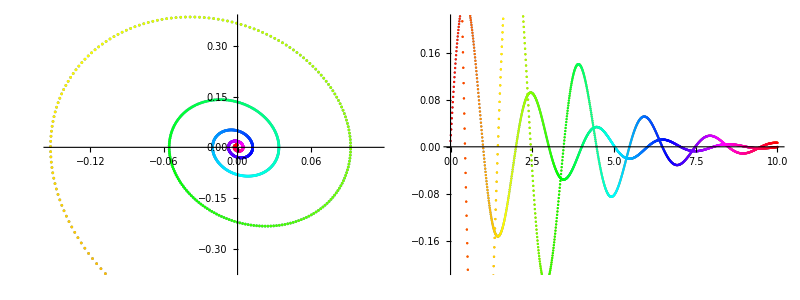

```mathematica
Module[{dt=0.01,t0=0,tN=10,times},
times=Range[t0,tN,dt];
With[{soln=Module[{m=1, k=10,ν=1,mat },mat=({{0, 1}, {-k/m, -ν/m}});
FoldList[
rk4stepA[#1,{ψ,t}↦mat.ψ,#2,dt]&,(* calculate one step *)
{0,1},(* initial state *)
times]]},
Grid[{
{ListPlot[MapIndexed[Style[#1,Hue[#2/len@soln]]&]@soln,ImageSize->Medium],
ListPlot[{
MapIndexed[Style[#1,Hue[#2/len@times]]&]@Transpose[{times,d1[pick[1]/@soln]}],
MapIndexed[Style[#1,Hue[#2/len@times]]&]@Transpose[{times,d1[pick[2]/@soln]}]},ImageSize->Medium]}
}]]]
```

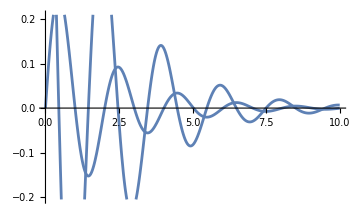

```mathematica
Module[{dt=0.01,t0=0,tN=10,times},
times=Range[t0,tN,dt];
With[{soln=Module[{m=1,k=10,ν=1},
NDSolve[{x''[t]==-k x[t]/m-ν x'[t]/m,x[0]==0,x'[0]==1},x,{t,0,10}]]},
Grid[{{Plot[{x[t],x'[t]}/.soln,{t,0,10},ImageSize->Medium]}}]]]
```

Demonstration that rk2step also matches NDSolve.

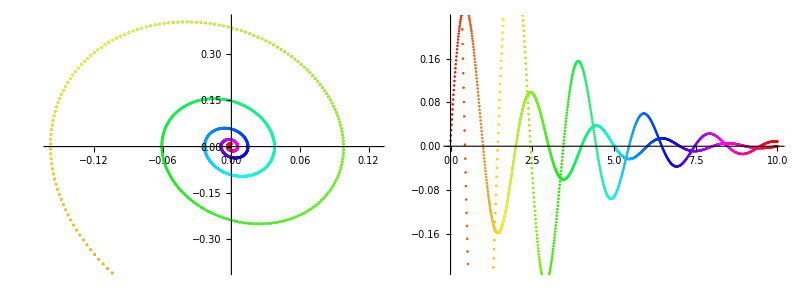

```mathematica
Module[{dt=0.01,t0=0,tN=10,times},
times=Range[t0,tN,dt];
With[{soln=Module[{m=1,k=10,ν=1,mat,ϕ},
mat=({{0, 1}, {-k/m, -ν/m}});
ϕ=Function[{ψ,t},mat];
FoldList[rk2step[#1,ϕ,#2,dt]&,{0,1},times]]},
Grid[{{
ListPlot[MapIndexed[Style[#1,Hue[#2/len@soln]]&]@soln,ImageSize->Medium],
ListPlot[{
MapIndexed[Style[#1,Hue[#2/len@times]]&]@Transpose[{times,d1[pick[1]/@soln]}],
MapIndexed[Style[#1,Hue[#2/len@times]]&]@Transpose[{times,d1[pick[2]/@soln]}]},ImageSize->Medium]}
}]]]
```

### Falling Object with Drag

My version of integrating the falling-object equation of motion with FoldList and rk2stepA, matching Zarchan & Musoff.

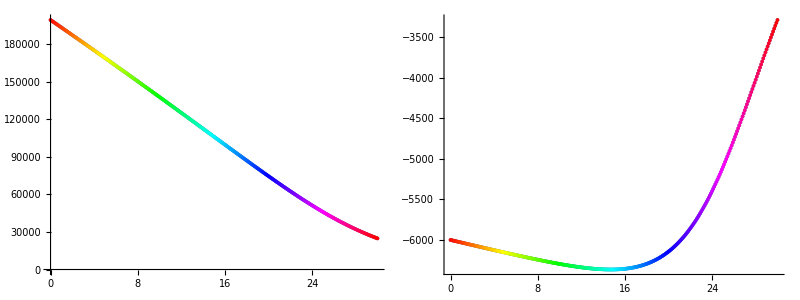

```mathematica
With[{g=32.2},
With[{x0=200000.,v0=-6000.,a0=-g,t0=0.,t1=30.,dt=.1},
Module[{times=Range[t0,t1,dt],timeStyler},
timeStyler[xs_]:=MapIndexed[Style[#1,Hue[#2/len@xs]]&];
With[{soln=
Module[{ρ,qp,β,drag,Dψ},
ρ[x_]:=0.0034 Exp[-x/22000];(* English units/g; Zarchan, P., 1998 *)
qp[{x_,v_}]:=0.5ρ[x] v^2;
β=500;
drag[ψ_]:=Sow[qp[ψ]g/β];
Dψ[ψ:{x_,v_},t_]:={v,a0+drag[ψ]};
FoldList[
eulerStepA[#1,Dψ,#2,dt]&,
{x0,v0},
times]]},
Grid[{
{ListPlot[{timeStyler[times]@Transpose[{times,d1[pick[1]/@soln]}]},ImageSize->Medium],
ListPlot[{timeStyler[times]@Transpose[{times,d1[pick[2]/@soln]}]},ImageSize->Medium]}
}]]]]]
```

#### Via NDSolve

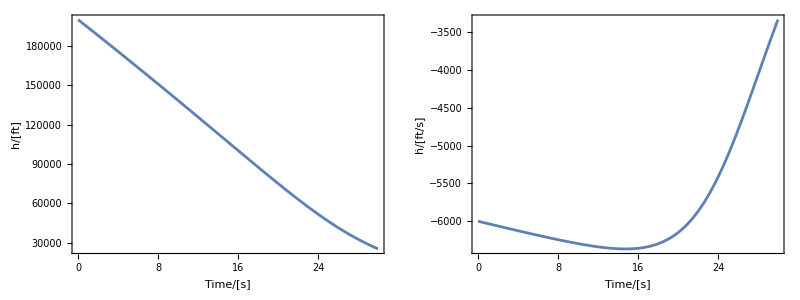

```mathematica
With[{g=32.2,A=0.0034,k=22000.,beta=500.},
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.},
With[{soln=NDSolve[{h''[t]==-g+A g (h'[t])^2 Exp[-h[t]/k]/(2.beta),
h[0]==x0,h'[0]==v0},h,{t,t0,t1}]},
Grid[{{Plot[h[t]/.soln,{t,t0,t1},
ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],
Plot[h'[t]/.soln,{t,t0,t1},
ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}]}}]]]]
```

#### Via Zarchan & Musoff

Page 229, fourth edition.

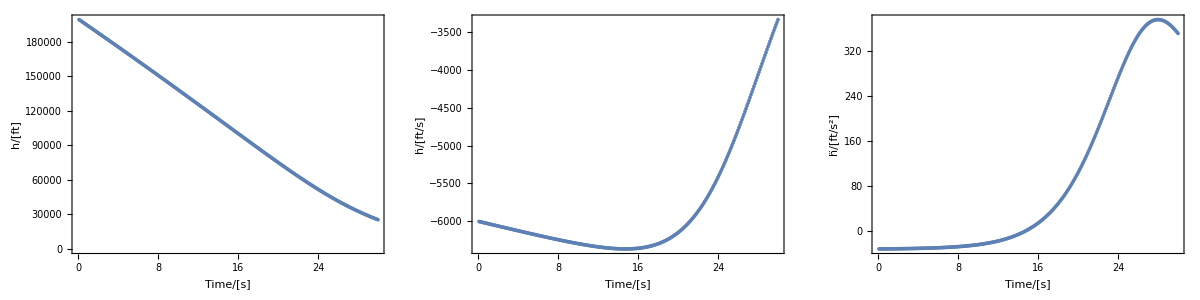

```mathematica
Module[{
g=32.2,
x=200000.,xd=-6000.,xdd,
xold,xdold,d,
beta=500.,
ts=.1,tf=30.,t=0,s=0,h=.001,
count=0,
arrayt,arrayx,arrayxd,arrayxdd},
{arrayt,arrayx,arrayxd,arrayxdd}=
Reap[
While[t<=tf,
xold=x;
xdold=xd;
xdd=0.0034g xd xd Exp[-x/22000.]/(2.beta)-g;
x=x+h xd;
xd=xd+h xdd;
t=t+h;
xdd=0.0034g xd xd Exp[-x/22000.]/(2.beta)-g;
x=0.5(xold+x+h xd);
d=0.5(xdold+xd+h xdd);
s=s+h;
If[s>ts-.00001,
s=0;
count=count+1;
Sow[t,"t"];
Sow[x,"x"];
Sow[xd,"xd"];
Sow[xdd,"xdd"]];]]⟦2⟧;
Grid[{{ListPlot[Transpose[{arrayt,arrayx}],
ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],
ListPlot[Transpose[{arrayt,arrayxd}],
ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}],
ListPlot[Transpose[{arrayt,arrayxdd}],
ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḧ/[ft/s^2]",""},{"Time/[s]","Acceleration vs. Time"}}]}}]]
```

#### Via Stream

## Streams Library

#### integersFrom

Let's make folds for potentially infinite, lazy, iteractive [sic] collections (streams). Represent a stream as a pair of a value and a thunk; the thunk must produce another stream.

Here's an example that produces the entire infinite set of integers:

```mathematica
integersFrom[n_Integer]:={n,integersFrom[n+1]&}
```

#### extract :: stream ⟶ value

Extract is a (tail-recursive) way to get the 1-indexed, n^th value from any stream.

By convention, a finite stream has a Null thunk at the end. Thus, the empty stream, obtained by invoking such a thunk, is Null[]. Extracting anything from such a stream produces, Null, which does not print in the notebook and looks like nothing.

```mathematica
ClearAll[extract];
(* defaulting n: *) 
extract[{v_,thunk_}]:=extract[{v,thunk},1];
(* base case: *) 
extract[Null[],_]:=Null; (* somebody invoked my null thunk! *)
(* do this if you just want the first value; it's the default *)
extract[{v_,thunk_},1]:=v;
(* tail recursion: *)
extract[{v_,thunk_},n_Integer/;n>1]:=extract[thunk[],n-1];
(* catch-all: *)extract[___]:=Null;
```

Now we can get the 630000-th integer efficiently (if not terribly quickly):

```mathematica
Block[{$IterationLimit=Infinity},
extract[integersFrom[1],630000]]//AbsoluteTiming
```

{0.640799,630000}

#### take :: stream ⟶ index ⟶ stream

Take a finite number of elements from a stream and produce another stream.

```mathematica
ClearAll[take];
take[stream_]:=take[stream,1];
take[_,0]:=Null[];
take[Null[],_]:=Null[];
take[{v_,thunk_},1]:={v,Null};
take[{v_,thunk_},n_Integer/;n>1]:={v,take[thunk[],n-1]&};
```

Produce a finite stream of three integers; extract the first value:

```mathematica
extract[take[integersFrom[1],3],1]
```

1

and the last value:

```mathematica
extract[take[integersFrom[1],3],3]
```

3

If we extract too far into a finite stream, we get Null, which doesn’t print to the notebook:

```mathematica
extract[take[integersFrom[1],3],4]
```

#### takeUntil :: stream ⟶ (value ⟶ Boolean) ⟶ stream

Take elements until some predicate evaluates to True, excluding that element.

```mathematica
ClearAll[takeUntil];
takeUntil[Null[],_]:=Null[];
takeUntil[{v_,thunk_},predicate_]/;predicate[v]:=Null[];
takeUntil[{v_,thunk_},predicate_]:={v,takeUntil[thunk[],predicate]&};
```

The example needs reify.

#### reify :: stream ⟶ list

Reify a stream to a list, invoking all thunks (not tail-recursive; might have to do better if we overflow the stack):

```mathematica
ClearAll[reify];
reify[Null[]]:={};
reify[{v_,Null}]:={v};
reify[{v_,thunk_}]:=Join[{v},reify[thunk[]]];
```

```mathematica
reify[take[integersFrom[1],3]]
```

{1,2,3}

```mathematica
reify[takeUntil[integersFrom[1],#>9&]]
```

{1,2,3,4,5,6,7,8,9}

#### disperse :: list ⟶ stream

```mathematica
ClearAll[disperse];
disperse[{}]:=Null[];
disperse[{x_}]:={x,Null};
disperse[{v_,xs__}]:={v,disperse[{xs}]&};
```

```mathematica
reify[disperse[{1,2,3}]]
```

{1,2,3}

```mathematica
reify[disperse[{}]]
```

{}

#### last :: stream ⟶ element

```mathematica
ClearAll[last];
last[Null[]]:=Null;
last[{v_,thunk_}/;thunk[]===Null[]]:=v;
last[{v_,thunk_}]:=last[thunk[]];
```

```mathematica
last@disperse[{}]
```

```mathematica
last@disperse[{1,2}]
```

2

```mathematica
Block[{$IterationLimit=Infinity},
last@take[integersFrom[1],630000]]//AbsoluteTiming
```

{1.94357,630000}

#### Fibonaccis as a Stream

Direct, non-tail recursive, fibonacci stream (with memoization, i.e., dynamic programming)

```mathematica
ClearAll[fibonaccis];
fibonaccis[0]={0,fibonaccis[2]&};
fibonaccis[1]={1,fibonaccis[3]&};
fibonaccis[n_]:=
(* Here's the dynamic programming: create a static value for a particular argument. *)
fibonaccis[n]=
{(* value *)
extract[fibonaccis[n-1]]+extract[fibonaccis[n-2]],
(* thunk *)
fibonaccis[n+1]&}
```

```mathematica
reify[take[fibonaccis[0],11]]
```

{0,1,2,3,5,8,13,21,34,55,89}

This is efficient, modulo stack overflow: it can find large Fibonacci numbers quickly:

```mathematica
extract[fibonaccis[0],200]//AbsoluteTiming
```

{0.000831,280571172992510140037611932413038677189525}

```mathematica
extract[fibonaccis[200]]//AbsoluteTiming
```

{2.×10^-6,280571172992510140037611932413038677189525}

#### foldStream :: f ⟶ initState ⟶ stream ⟶ stream

```mathematica
ClearAll[foldStream];
foldStream[f_,s_,Null[]]:={s,Null};
foldStream[f_,s_,{z_,thunk_}]:=
{s,foldStream[f,f[s,z],thunk[]]&};
```

```mathematica
allFibs=
foldStream[
{s,z}↦{s⟦2⟧,s⟦1⟧+s⟦2⟧},
{0,1},
integersFrom[0]];(* lazy stream: all ints *)
Transpose@reify@take[allFibs,11]//TeXForm(* don't take them all; that won't finish *)
```

\left(
\begin{array}{ccccccccccc}
 0 & 1 & 1 & 2 & 3 & 5 & 8 & 13 & 21 & 34 & 55 \\
 1 & 1 & 2 & 3 & 5 & 8 & 13 & 21 & 34 & 55 & 89 \\
\end{array}
\right)

Here is another Fibonacci stream:

```mathematica
MatrixForm/@
Module[{f=({{0, 1}, {1, 1}}),fs},
fs[fk_]:={fk,fs[fk.f]&};
reify@take[fs[IdentityMatrix@2],11]]
```

{(1 | 0
0 | 1),(0 | 1
1 | 1),(1 | 1
1 | 2),(1 | 2
2 | 3),(2 | 3
3 | 5),(3 | 5
5 | 8),(5 | 8
8 | 13),(8 | 13
13 | 21),(13 | 21
21 | 34),(21 | 34
34 | 55),(34 | 55
55 | 89)}

#### mapStream :: stream ⟶ unaryFunction ⟶ stream

```mathematica
ClearAll[mapStream];
mapStream[Null[],_]:=Null[];
mapStream[{v_,thunk_},f_]:={f[v],mapStream[thunk[],f]&};
```

```mathematica
reify@mapStream[disperse@{1,2,3},#^2&]
```

{1,4,9}

```mathematica
reify@mapStream[take[integersFrom[1],3],#^2&]
```

{1,4,9}

#### forEach :: stream ⟶ unaryFunction ⟶ Null

forEach takes a stream and a unary function and invokes the function on every member of the stream for side effect.

Don’t invoke this on infinite stream, as with reify.

```mathematica
ClearAll[forEach];
forEach[Null[],lambda_]:=Null;
forEach[{v_,thunk_},lambda_]:=
(lambda[v](* discard lambda's result *);forEach[thunk[],lambda];);
```

an example, side-effecting the notebook via Print:

```mathematica
forEach[take[allFibs,11],Print]
```

{0,1}

{1,1}

{1,2}

{2,3}

{3,5}

{5,8}

{8,13}

{13,21}

{21,34}

{34,55}

{55,89}

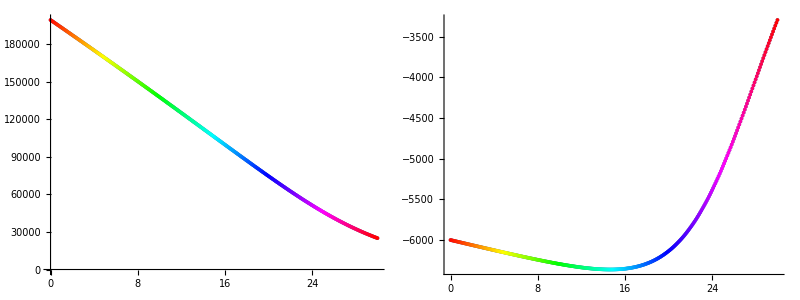

```mathematica
With[{g=32.2,A=0.0034,k=22000.,beta=500.},
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.,dt=.1},
Module[{times=Range[t0,t1,dt],timeStyler},
timeStyler[xs_]:=MapIndexed[Style[#1,Hue[#2/len@xs]]&];
With[{soln=
Module[{Dψ},
Dψ[ψ:{x_,v_},t_]:={v,-g+A g Exp[-x/k]v^2/(2beta)};
FoldList[
rk4stepA[#1,Dψ,#2,dt]&,
{x0,v0},
times]]},
Grid[{
{ListPlot[{timeStyler[times]@Transpose[{times,d1[pick[1]/@soln]}]},ImageSize->Medium],
ListPlot[{timeStyler[times]@Transpose[{times,d1[pick[2]/@soln]}]},ImageSize->Medium]}
}]]]]]
```

```mathematica
slug/ft^3(ft/sec)^2
```

slug/(ft sec^2)

```mathematica
(slug ft)/sec^2/ft^2
```

slug/(ft sec^2)

#### Without a stream integrator

```mathematica
ClearAll[dragStream];
(* Let-Over-Lambda style: *)
With[{g=32.2,A=0.0034,k=22000.,beta=500.},
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.,dt=.1},
Module[{Dψ},
Dψ[ψ:{x_,v_},t_]:={v,-g-A g Exp[-x/k]v^2/(2beta)};
dragStream[ψ:{δt_,t_,x_,v_}]:=
{ψ,dragStream[{δt,t+δt}⊕rk4stepA[{x,v},Dψ,t,δt]]&}]]];
```

#### Abstracting a non-stream integrator

```mathematica
ClearAll[dragStream];
With[{integrator=eulerStepA,g=32.2,beta=500},
Module[{Dx},Dx[{x_,v_},t_]:={v,g(0.0034 Exp[-x/22000]v^2/(2.beta)-1)};
dragStream[psi:{dt_,t_,x_,v_}]:=
{psi,dragStream[{dt,t+dt}~Join~integrator[{x,v},Dx,t,dt]]&}]];
```

```mathematica
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.,dt=.1},
reify[
takeUntil[
dragStream[{dt,t0,x0,v0}],#⟦2⟧>.3&]]]
```

{{0.1,0.,200000.,-6000.},{0.1,0.1,199400.,-6003.18},{0.1,0.2,198800.,-6006.35},{0.1,0.3,198199.,-6009.52}}

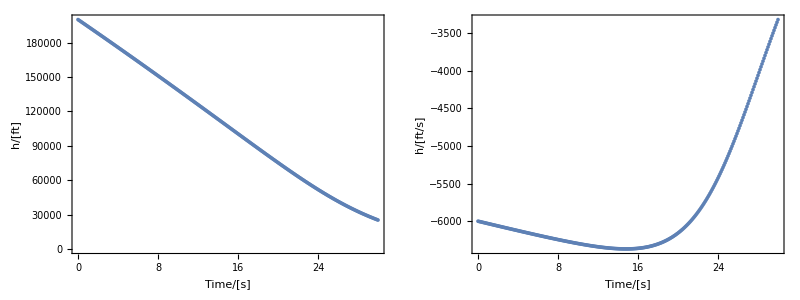

```mathematica
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.,dt=.1},
Module[{ts,xs,vs},
{ts,xs,vs}=Transpose[#⟦2;;4⟧&/@
reify[
takeUntil[
dragStream[{dt,t0,x0,v0}],#⟦2⟧>30.&]]];
Grid[{
{ListPlot[{Transpose[{ts,xs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],
ListPlot[{Transpose[{ts,vs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}]}}]]]
```

Can we take a stream that implements differentials, foldStream an integrator over it, and get a stream that implements the integrated differential equation?

```mathematica
ClearAll[eulerAccumulator,rk2Accumulator,rk4Accumulator,dragD,dragDStream];
eulerAccumulator[{t_,x_},{dt_,t_,Dx_}]:=
{t+dt,x+dt Dx[x,t]};
rk2Accumulator[{t_,x_},{dt_,t_,Dx_}]:=
With[{dx1=dt Dx[x,t]},
With[{dx2=dt Dx[x+.5dx1,t+.5dt]},
{t+dt,x+(dx1+dx2)/2.}]];
rk4Accumulator[{t_,x_},{dt_,t_,Dx_}]:=
With[{dx1=dt Dx[x,t]},
With[{dx2=dt Dx[x+.5dx1,t+.5dt]},
With[{dx3=dt Dx[x+.5dx2,t+.5dt]},
With[{dx4=dt Dx[x+dx3,t+dt]},
{t+dt,x+(dx1+2.dx2+2.dx3+dx4)/6.}]]]];
With[{g=32.2,A=0.0034,k=22000.,beta=500.},(* let-over-lambda style *)
dragD[{x_,v_},t_]:={v,g(A Exp[-x/k]v^2/(2.beta)-1)}];
dragDStream[Δ:{dt_,t_,Dx_}]:={Δ,dragDStream[{dt,t+dt,Dx}]&};
```

```mathematica
reify[
With[{x0=200000.,v0=-6000.,t0=0.,t1=0.3,dt=.1},
takeUntil[
foldStream[
rk4Accumulator,
{t0,{x0,v0}},
dragDStream[{dt,t0,dragD}]
],First[#]>t1&]]]
```

{{0.,{200000.,-6000.}},{0.1,{199400.,-6003.17}},{0.2,{198799.,-6006.35}},{0.3,{198199.,-6009.52}}}

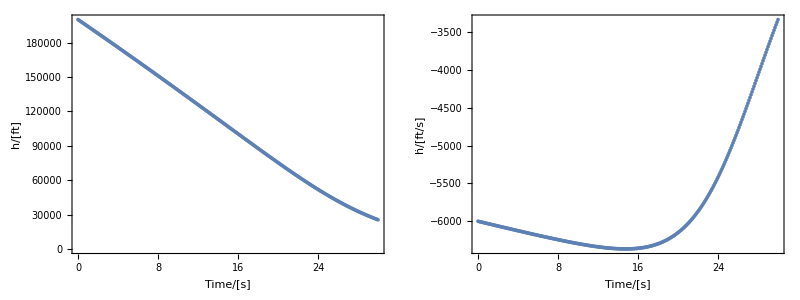

```mathematica
With[{soln=
reify[
With[{x0=200000.,v0=-6000.,t0=0.,t1=30.,dt=.1},
takeUntil[
foldStream[
rk4Accumulator,
{t0,{x0,v0}},
dragDStream[{dt,t0,dragD}]
],First[#]>t1&]]]},
Module[{ts,ps,xs,vs},
{ts,ps}=Transpose[soln];
{xs,vs}=Transpose[ps];
Grid[{
{ListPlot[{Transpose[{ts,xs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],
ListPlot[{Transpose[{ts,vs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}]}}]]]
```

## Linearization

```mathematica
((ρ[x] v^2)/(2β)-1)g
```

g (-1+(v^2 ρ[x])/(2 β))

```mathematica
ρRule={ρ[x_]:>34/10000 Exp[x/22000]}
```

{ρ[x_]:>(34 Exp[x/22000])/10000}

```mathematica
D[((ρ[x] v^2)/(2β)-1)g/.ρRule,x]
```

(17 ⅇ^(x/22000) g v^2)/(220000000 β)

```mathematica
D[((ρ[x] v^2)/(2β)-1)g/.ρRule,v]
```

(17 ⅇ^(x/22000) g v)/(5000 β)

```mathematica
ρRule={ρ[x_]:>A Exp[-x/k]}
```

{ρ[x_]:>A Exp[-x/k]}

```mathematica
D[((ρ[x] v^2)/(2β)-1)g/.ρRule,x]//TeXForm
```

-\frac{A g v^2 e^{-\frac{x}{k}}}{2 \beta  k}

```mathematica
D[((ρ[x] v^2)/(2β)-1)g/.ρRule,v]//TeXForm
```

\frac{A g v e^{-\frac{x}{k}}}{\beta }

```mathematica
f21=D[((ρ[x] v^2)/(2β)-1)g/.ρRule,x]
```

-(A ⅇ^(-x/k) g v^2)/(2 k β)

```mathematica
<<"Units`"
```

```mathematica
f21/.(unitRules={x->Foot,k->Foot,g->Foot/Second^2,v->Foot/Second,A->Slug/Foot^3,β->(Slug Foot)/Second^2/Foot^2})
```

-1/(2 ⅇ Second^2)

```mathematica
f22=D[((ρ[x] v^2)/(2β)-1)g/.ρRule,v]
```

(A ⅇ^(-x/k) g v)/β

```mathematica
f22/.unitRules
```

1/(ⅇ Second)

```mathematica
((ρ v^2)/(2β)-1)g/.unitRules/.{ρ->Slug/Foot^3}
```

-Foot/(2 Second^2)

```mathematica
ClearAll[Φ];
Φ[τ_]:=(id[2]+(F=({{0, 1}, {F21, F22}}))τ)
```

```mathematica
Integrate[Φ[t].({{0, 0}, {0, 1}}).Φ[t]ᵀ,{t,0,dt}]//FullSimplify//MatrixForm
```

(dt^3/3 | 1/6 dt^2 (3+2 dt F22)
1/6 dt^2 (3+2 dt F22) | dt+dt^2 F22+(dt^3 F22^2)/3)

```mathematica
Integrate[Φ[t].({{0, 0}, {0, 1}}).Φ[t]ᵀ,{t,0,dt}]//MatrixForm
```

(dt^3/3 | dt^2/2+(dt^3 F22)/3
dt^2/2+(dt^3 F22)/3 | dt+dt^2 F22+(dt^3 F22^2)/3)

## EKF Interactive

### Experiment by hand

```mathematica
ClearAll[Phi,Xi];
```

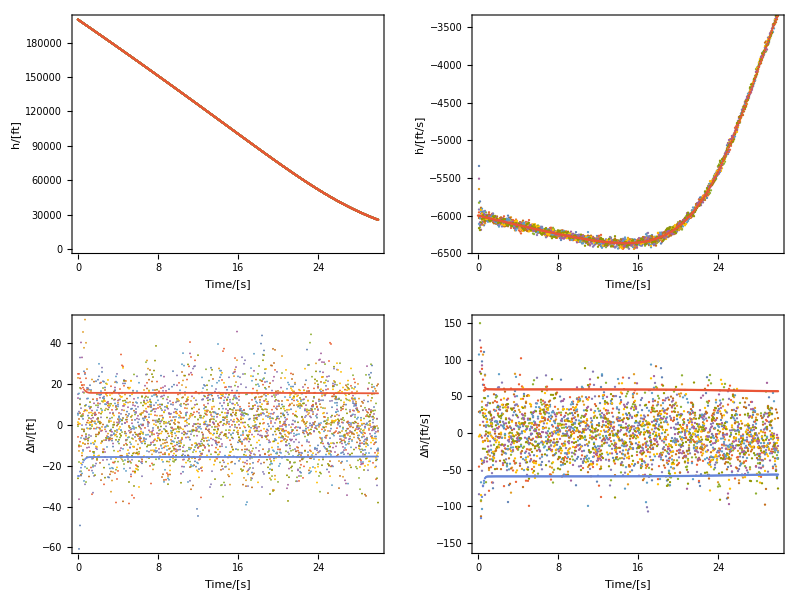

```mathematica
With[{g=32.2,A=0.0034,k=22000.,beta=500.},
Module[{dragD,dragDStream,F21,F22,Phi,Xi,EKFDrag},
dragD[{x_,v_},t_]:={v,g(A Exp[-x/k]v^2/(2.beta)-1)};
dragDStream[Delta:{dt_,t_,Dx_}]:={Delta,dragDStream[{dt,t+dt,Dx}]&};
F21[x_,v_]:=-A Exp[-x/k]g v^2/(2. k beta);
F22[x_,v_]:=A Exp[-x/k]g v/beta;
Phi[dt_,{x_,v_}]:={{1,dt},{dt*F21[x,v],1+dt*F22[x,v]}};
Xi[dt_,{x_,v_}]:=With[{f=F22[x,v]},
{{dt^3/3,(dt^2*(3+2*dt*f))/6},{(dt^2*(3+2*dt*f))/6,dt+dt^2*f+(dt^3*f^2)/3}}];
EKFDrag[sigmaXi_,Zeta_,integrator_,fdt_,idt_][{x_,P_},{t_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=last[takeUntil[foldStream[integrator,{t,x},
dragDStream[{idt,t,dragD}]],
First@#>t+fdt&]]⟦2⟧;
P2=sigmaXi^2 Xi[fdt,x]+Phi[fdt,x].P.Phi[fdt,x]ᵀ;
D=Zeta+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
With[{nStates=2,nIterations=10},
With[{sigmaZeta=25.,sigmaXi=100.0,t0=0.,t1=30.,filterDt=0.1,integrationDt=0.1},
With[{x0=200000,v0=-6000,Ζ=sigmaZeta^2 id[1],P0=1000000000000id[nStates]},
Module[{fakes},
fakes[]:=foldStream[rk4Accumulator,{t0,{x0,v0}},
dragDStream[{filterDt,t0,dragD}]];
SeedRandom[44];
Module[{ffs,rffs,ts,xvs,xss,vss,txs,tvs,ps,σxs,σvs},
xss=ConstantArray[0,nIterations];
vss=ConstantArray[0,nIterations];
ffs=takeUntil[fakes[],First@#>t1&];
rffs=reify@ffs;
ts=pick[1]/@rffs;
txs=pick[2,1]/@rffs;
tvs=pick[2,2]/@rffs;
{xss,vss}=Transpose@Map[
({xvs,ps}=Transpose@Rest@reify@foldStream[
EKFDrag[sigmaXi,Ζ,rk2Accumulator,filterDt,integrationDt],
{{0,0},P0},
mapStream[ffs,{#⟦1⟧,({{1, 0}}),#⟦2,1⟧+gen[Ζ]}&]];
σxs=If[Not[ValueQ[σxs]],Sqrt[pick[1,1]/@ps],σxs];
σvs=If[Not[ValueQ[σvs]],Sqrt[pick[2,2]/@ps],σvs];
Transpose@xvs)&,
Range[nIterations]];
Grid[{
{ListPlot[Transpose/@({ts,#}&/@xss)⊕{Transpose[{ts,txs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],ListPlot[Transpose/@({ts,#}&/@vss)⊕{Transpose[{ts,tvs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}]},
{ListPlot[Transpose/@({ts,txs-#}&/@xss)⊕{Transpose[{ts,σxs}],Transpose[{ts,-σxs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"Δh/[ft]",""},{"Time/[s]","Height Residual vs. Time"}}],ListPlot[Transpose/@({ts,tvs-#}&/@vss)⊕{Transpose[{ts,σvs}],Transpose[{ts,-σvs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"Δḣ/[ft/s]",""},{"Time/[s]","Speed Residual vs. Time"}}]}}]
]]
]]]]]
```

### Manipulator

```mathematica
Manipulate[
With[{g=32.2,A=0.0034,k=22000.,beta=500.},
Module[{dragD,dragDStream,F21,F22,Phi,Xi,EKFDrag},
dragD[{x_,v_},t_]:={v,g(A Exp[-x/k]v^2/(2.beta)-1)};
dragDStream[Delta:{dt_,t_,Dx_}]:={Delta,dragDStream[{dt,t+dt,Dx}]&};
F21[x_,v_]:=-A Exp[-x/k]g v^2/(2. k beta);
F22[x_,v_]:=A Exp[-x/k]g v/beta;
Phi[dt_,{x_,v_}]:={{1,dt},{dt*F21[x,v],1+dt*F22[x,v]}};
Xi[dt_,{x_,v_}]:=With[{f=F22[x,v]},
{{dt^3/3,(dt^2*(3+2*dt*f))/6},{(dt^2*(3+2*dt*f))/6,dt+dt^2*f+(dt^3*f^2)/3}}];
EKFDrag[sigmaXi_,Zeta_,integrator_,fdt_,idt_][{x_,P_},{t_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=last[takeUntil[foldStream[integrator,{t,x},
dragDStream[{idt,t,dragD}]],
First@#>t+fdt&]]⟦2⟧;
P2=sigmaXi^2 Xi[fdt,x]+Phi[fdt,x].P.Phi[fdt,x]ᵀ;
D=Zeta+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
Block[{$IterationLimit=Infinity},
With[{nStates=2},
With[{t0=0.,t1=30.,filterDt=0.1},
With[{x0=200000,v0=-6000,Ζ=sigmaZeta^2 id[1],P0=1000000000000id[nStates]},
Module[{fakes,integrators={eulerAccumulator,rk2Accumulator,rk4Accumulator},
integrationDt},
fakes[]:=foldStream[rk4Accumulator,{t0,{x0,v0}},
dragDStream[{filterDt,t0,dragD}]];
integrationDt=10.0^logIntegratorDt;
SeedRandom[randomSeed];
Module[{ffs,rffs,ts,xvs,xss,vss,txs,tvs,ps,σxs,σvs},
xss=ConstantArray[0,nIterations];
vss=ConstantArray[0,nIterations];
ffs=takeUntil[fakes[],First@#>t1&];
rffs=reify@ffs;
ts=pick[1]/@rffs;
txs=pick[2,1]/@rffs;
tvs=pick[2,2]/@rffs;
{xss,vss}=Transpose@Map[
({xvs,ps}=Transpose@Rest@reify@foldStream[
EKFDrag[sigmaXi,Ζ,integrators[[integrator]],filterDt,integrationDt],
{{0,0},P0},
mapStream[ffs,{#⟦1⟧,({{1, 0}}),#⟦2,1⟧+gen[Ζ]}&]];
σxs=If[Not[ValueQ[σxs]],Sqrt[pick[1,1]/@ps],σxs];
σvs=If[Not[ValueQ[σvs]],Sqrt[pick[2,2]/@ps],σvs];
Transpose@xvs)&,
Range[nIterations]];
Grid[{
{ListPlot[Transpose/@({ts,#}&/@xss)⊕{{ts,txs}ᵀ},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"h/[ft]",""},{"Time/[s]","Height vs. Time"}}],ListPlot[Transpose/@({ts,#}&/@vss)⊕{{ts,tvs}ᵀ},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"ḣ/[ft/s]",""},{"Time/[s]","Speed vs. Time"}}]},
{ListPlot[Transpose/@({ts,txs-#}&/@xss)⊕{Transpose[{ts,σxs}],Transpose[{ts,-σxs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"Δh/[ft]",""},{"Time/[s]","Height Residual vs. Time"}}],ListPlot[Transpose/@({ts,tvs-#}&/@vss)⊕{Transpose[{ts,σvs}],Transpose[{ts,-σvs}]},ImageSize->Medium,GridLines->Full,Frame->True,
FrameLabel->{{"Δḣ/[ft/s]",""},{"Time/[s]","Speed Residual vs. Time"}}]}}]]
]]
]]]]],
Grid[{{Control[{{sigmaZeta,25},1,1000,1,Appearance->"Open"}], Control[{{sigmaXi,0},0,1000,1,Appearance->"Open"}]}, {Control[{{nIterations,2},1,25,1,Appearance->"Open"}], Control[{{randomSeed,42},42,142,1,Appearance->"Open"}]}, {Control[{{integrator,1},1,3,1,Appearance->"Open"}], Control[{{logIntegratorDt,-1},-6,-1,1,Appearance->"Open"}]}}]]
```

Set::shape: Lists {xvs$158558,ps$158558} and Transpose[reify[]] are not the same shape.

#### Via Zarchan & Musoff [UNFINISHED]

Not much point in finishing this as I reproduced their results with an Euler integrator!

```mathematica
(*Module[{signoise,x,xd,beta,xh,xdh,order,ts,tf,phis,t,s,h,p,idnp,hmat,rmat,count,xold,xdold,xdd,rho,f21,f22,f,phi,q,m,k,xnoise,xddb,xdb,xb,res,errx,sp11,errxd,sp22,sp11p,sp22p,arrayt,arrayx,arrayxh,arrayxd,arrayxdh,arrayerrx,arraysp11,arraysp11p,arrayerrxd,arraysp22,arraysp22p},
signoise=1000.;
x=200000.;
xd=-6000.;
beta=500.;
xh=200025.;
xdh=6150.;
order=2;
ts=.1;
tf=30.;
phis=0./tf;
t=0.;
s=0.;
h=0.001;
p=({{signoise^2, 0}, {0., 20000}});
idnp=id[order];
hmat=({{1, 0}});
rmat=signoise^2;
count=0;
{arrayt,arrayx,arrayxh,arrayxd,arrayxdh,arrayerrx,arraysp11,arraysp11p,arrayerrxd,arraysp22,arraysp22p}=
Reap@While[t≤tf,
xold=x;
xdold=xd;
xdd=.0034 32.2 xd xd Exp[-x/22000.]/(2.beta)-32.2;
x=x+h*xd;
xd=xd+h xdd;
]⟦2⟧;
]*)
```

## Non-Dimensionalization

```mathematica
ClearAll[x,v,t,A,F,f11,f12,f21,f22];
```

```mathematica
DSolve[{Dt[x[t],t]==F x[t],x[0]==A},x,t]
```

{{x→Function[{t},A ⅇ^(F t)]}}

```mathematica
soln$=DSolve[x''[t]==a x[t]+b x'[t],x,t]
```

{{x→Function[{t},ⅇ^(1/2 (b-√(4 a+b^2)) t) C[1]+ⅇ^(1/2 (b+√(4 a+b^2)) t) C[2]]}}

```mathematica
D[(x/.soln$)[[1]][t],{t,2}]-a (x/.soln$)[[1]][t]-b D[(x/.soln$)[[1]][t],t]//FullSimplify
```

0

```mathematica
DSolve[Dt[{{x'[t]}},t]==({{a, b}}).({{x[t]}, {x'[t]}}),x,t]
```

{{x→Function[{t},ⅇ^(1/2 (b-√(4 a+b^2)) t) C[1]+ⅇ^(1/2 (b+√(4 a+b^2)) t) C[2]]}}

```mathematica
DSolve[
```

## ExperimentEKF

```mathematica
ClearAll[experimentEKF];
experimentEKF[filter_,
startTime_,endTime_,timeIncrement_,
aPrioriState_,aPrioriCovariance_,fakeFn_,
nStates_Integer:2,truthFns_List:{Identity,Identity},
labelsPacket_List:stir@labelsPacket2[{"Independent Variable","?dim"},{{"State1","?dim"},{"State2","?dim"}}],
statsLabels_List:{"State1","State2"},iterations_Integer:1]:=
Module[{t,timesIter,times,fakes,estss,
trueStates,estimatedStatess,residualStatess,
stddevStatess,theoStateVarss,statsStates,styler},
styler=myStyle/@#&;
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
trueStates=Table[truthFns⟦n⟧[t],{n,nStates},Evaluate@timesIter];
fakes[]:=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
estss=Table[
FoldList[filter,{aPrioriState,aPrioriCovariance},fakes[]],
iterations];
(* starts at 2;; to skip the a-priori *)
estimatedStatess=Table[estss⟦;;,2;;,1,n,1⟧,{n,nStates}];
residualStatess=Table[trueStates⟦n⟧-#&/@estimatedStatess⟦n⟧,{n,nStates}];
stddevStatess=Table[sqrt@estss⟦(;;),(2;;),2,n,n⟧,{n,nStates}];
theoStateVarss=Table[Last[estss⟦1⟧]⟦2,n,n⟧,{n,nStates}];
statsStates=Table[stats[statsLabels⟦n⟧,
f1@residualStatess⟦n⟧,f1@stddevStatess⟦n⟧,theoStateVarss⟦n⟧],{n,nStates}];
Grid@{Table[ListLinePlot[(withTimes[times,#]&/@residualStatess⟦n⟧)⊕
(withTimes[times,#]&/@stddevStatess⟦n⟧)⊕
(withTimes[times,#]&/@-stddevStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
Table[ListLinePlot[{withTimes[times,trueStates⟦n⟧]}⊕
(withTimes[times,#]&/@estimatedStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n+nStates⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
statsStates}];
```

## Three-State Accelerometer

### With P ← L.P

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Kᵀ;
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P1(*P2-K.D.Kᵀ*)}];
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°,θ0=0.,θ1=180.°,
nStates=3,nIterations=1,nDisturbances=1},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{Ξ=zero[nStates],Φ=zero[nStates],Γ=zero[nStates,nDisturbances],u=zero[nDisturbances]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[nStates,1],aPrioriCovariance=99999999999id[nStates]},
Module[{Ζ,zees,partials},
Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦
With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy],Ξ,Φ,Γ,u,
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
nStates,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],
{"Bias","Scale","Drift"},nIterations],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]]
```

{{{{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 86.9565
Bias resids >= σ | 7.
Bias resids < σ | 80.
average Bias resid | 0.0113483
theoretical std dev | 5.08884×10^-6
std dev of Bias resids | 0.114917 | % Scale resids < σ (Expect >= 68) | 61.9565
Scale resids >= σ | 30.
Scale resids < σ | 57.
average Scale resid | -0.000714109
theoretical std dev | 9.08003×10^-8
std dev of Scale resids | 0.00717694 | % Drift resids < σ (Expect >= 68) | 85.8696
Drift resids >= σ | 8.
Drift resids < σ | 79.
average Drift resid | 0.0000112456
theoretical std dev | 6.39081×10^-9
std dev of Drift resids | 0.000112081,{-Graphics-}},{-Graphics-}},{-Graphics-}}}

## Two-State Falling Object

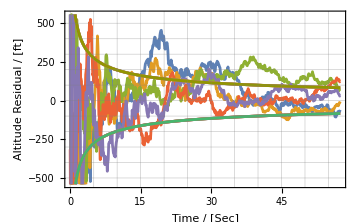
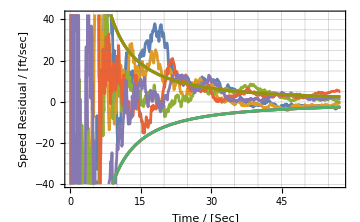
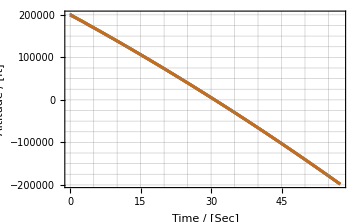
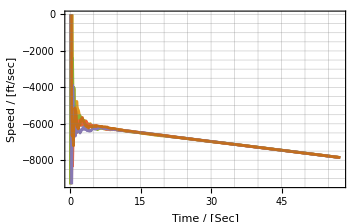
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% Altitude resids < σ (Expect >= 68) | 67.5694
Altitude resids >= σ | 934.
Altitude resids < σ | 1946.
average Altitude resid | 23.3447
theoretical std dev | 83.2249
std dev of Altitude resids | 176.498 | % Speed resids < σ (Expect >= 68) | 71.9792
Speed resids >= σ | 807.
Speed resids < σ | 2073.
average Speed resid | -76.0119
theoretical std dev | 2.50586
std dev of Speed resids | 1218.84

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L},
x2=Φ.x+Γ.u;P2=Ξ+Φ.P.Φᵀ;D=Ζ+A.P2.Aᵀ;K=P2.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
{x2+K.(z-A.x2),L.P2}];
With[{g=32.2,αsh=22000(* atmospheric scale height [ft] *)},
With[{x0=200000,v0=-6000,a0=-g,σz=1000.,σx=0.,nStates=2,nDisturbances=1,nIterations=5},
Module[{ρ,qp,β,drag,Dψ},
ρ[x_]:=0.0034 Exp[-x/αsh];(* English units/g; Zarchan, P., 1998 *)
qp[{x_,v_}]:=0.5ρ[x] v^2;β=500;drag[ψ_]:=qp[ψ]g/β;
Dψ[ψ:{x_,v_},t_]:={v,a0+drag[ψ]};
Module[{f21,f22},
f21[ψ:{x_,v_}]:=(-ρ[x] v^2)/(2αsh β);
f22[ψ:{x_,v_}]:=(ρ[x]x)/β;
With[{Ξ=zero[nStates],Φ=zero[nStates],Γ=zero[nStates,nDisturbances],u=zero[nDisturbances]},
With[{aPrioriState=zero[nStates,1],aPrioriCovariance=99999999999id[nStates],
Ζ=col[{σz^2}]},
SeedRandom[42];
experimentTDZ[0,57.5,0.1,aPrioriState,aPrioriCovariance,
{dt,t}↦
{Ζ,σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),({{1, dt}, {0, 1}}),({{dt^2/2}, {dt}}),col[{a0}],({{1, 0}}),
col[{x0+v0 t+a0 t^2/2}]+gen[Ζ]},nStates,
{t↦x0+v0 t+a0 t^2/2, (* true position *)
t↦v0+a0 t },
stir@labelsPacket2[{"Time","Sec"},{{"Altitude","ft"},{"Speed","ft/sec"}}],
{"Altitude","Speed"},nIterations]]]]]]]
```

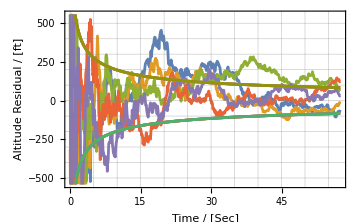
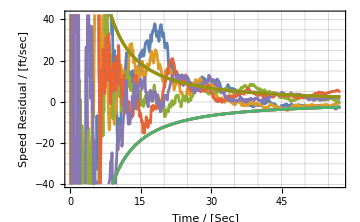
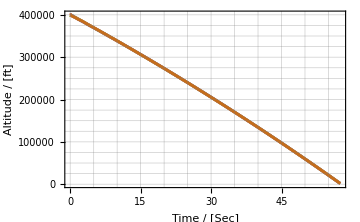
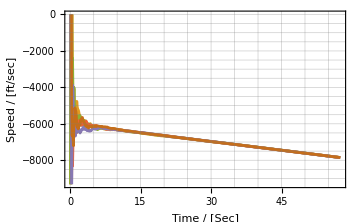
-Graphics- | -Graphics-
-Graphics- | -Graphics-
% Altitude resids < σ (Expect >= 68) | 67.5694
Altitude resids >= σ | 934.
Altitude resids < σ | 1946.
average Altitude resid | 23.3069
theoretical std dev | 83.2249
std dev of Altitude resids | 176.536 | % Speed resids < σ (Expect >= 68) | 71.9792
Speed resids >= σ | 807.
Speed resids < σ | 2073.
average Speed resid | -110.598
theoretical std dev | 2.50586
std dev of Speed resids | 1982.94

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K,L},
x2=Φ.x+Γ.u;P2=Ξ+Φ.P.Φᵀ;D=Ζ+A.P2.Aᵀ;K=P2.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
{x2+K.(z-A.x2),L.P2}];
With[{x0=400000,v0=-6000,g=-32.2,σz=1000.,σx=0.,nStates=2,nDisturbances=1,nIters=5},
With[{Ξ=zero[nStates],Φ=zero[nStates],Γ=zero[nStates,nDisturbances],u=zero[nDisturbances]},
With[{aPrioriState=zero[nStates,1],aPrioriCovariance=99999999999id[nStates],
Ζ=col[{σz^2}]},
SeedRandom[42];
experimentTDZ[0,57.5,0.1,aPrioriState,aPrioriCovariance,
{dt,t}↦
{Ζ,σx^2({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),({{1, dt}, {0, 1}}),({{dt^2/2}, {dt}}),col[{g}],({{1, 0}}),
col[{x0+v0 t+g t^2/2}]+gen[Ζ]},nStates,
{t↦x0+v0 t+g t^2/2, (* true position *)
t↦v0+g t },
stir@labelsPacket2[{"Time","Sec"},{{"Altitude","ft"},{"Speed","ft/sec"}}],
{"Altitude","Speed"},nIters]]]]
```